# MagicStatePrep simulation data

## Configuration

```mathematica
CloudConnect[]
```

chamber@caltech.edu

```mathematica
ResourceFunction["MaTeXInstall"][]
```

Paclet[MaTeX,1.7.5,<>]

```mathematica
ParentDirectory[]
```

/Users

```mathematica
ConfigureMaTeX["pdfLaTeX"->"/Library/TeX/texbin/pdflatex","Ghostscript"->"/usr/local/bin/gs"]
```

ConfigureMaTeX[pdfLaTeX→/Library/TeX/texbin/pdflatex,Ghostscript→/usr/local/bin/gs]

```mathematica
Needs["MaTeX`"];
```

## Color code total logical failure rate

```mathematica
(*Total number of qubits for Chamberland-Kubica color code*)
TotalNumQubitsCKcolor[d_]:=(3*d-1)^2/4;
```

### Import data

```mathematica
data3Dd5=Import["/Users/appleuser/Dropbox/IBM/ShortTermProjects/ColorCodePaper/data/colorcode3D_distance5","Table"];
data3Dd7=Import["/Users/appleuser/Dropbox/IBM/ShortTermProjects/ColorCodePaper/data/colorcode3D_distance7","Table"];
data3Dd9=Import["/Users/appleuser/Dropbox/IBM/ShortTermProjects/ColorCodePaper/data/colorcode3D_distance9","Table"];
data3Dd11=Import["/Users/appleuser/Dropbox/IBM/ShortTermProjects/ColorCodePaper/data/colorcode3D_distance11","Table"];
data3Dd13=Import["/Users/appleuser/Dropbox/IBM/ShortTermProjects/ColorCodePaper/data/colorcode3D_distance13","Table"];
data3Dd15=Import["/Users/appleuser/Dropbox/IBM/ShortTermProjects/ColorCodePaper/data/colorcode3D_distance15","Table"];
```

### Create data matrix

```mathematica
logicX3Dd5=Table[{data3Dd5[[i,1]],data3Dd5[[i+1,1]]},{i,5,Dimensions[data3Dd5][[1]]-2,3}]
logicZ3Dd5=Table[{data3Dd5[[i,1]],data3Dd5[[i+1,2]]},{i,5,Dimensions[data3Dd5][[1]]-2,3}]
logicY3Dd5=Table[{data3Dd5[[i,1]],data3Dd5[[i+1,3]]},{i,5,Dimensions[data3Dd5][[1]]-2,3}]
logicTot3Dd5=Table[{data3Dd5[[i,1]],data3Dd5[[i+1,4]]},{i,5,Dimensions[data3Dd5][[1]]-2,3}]
EBarlogicX3Dd5=Table[{data3Dd5[[i,1]],data3Dd5[[i+2,1]]},{i,5,Dimensions[data3Dd5][[1]]-2,3}]
EBarlogicZ3Dd5=Table[{data3Dd5[[i,1]],data3Dd5[[i+2,2]]},{i,5,Dimensions[data3Dd5][[1]]-2,3}]
EBarlogicY3Dd5=Table[{data3Dd5[[i,1]],data3Dd5[[i+2,3]]},{i,5,Dimensions[data3Dd5][[1]]-2,3}]
EBarlogicTot3Dd5=Table[{data3Dd5[[i,1]],data3Dd5[[i+2,4]]},{i,5,Dimensions[data3Dd5][[1]]-2,3}]
```

{{0.0003,0.000276},{0.0004,0.000641},{0.0005,0.001228},{0.0006,0.002173},{0.0007,0.003271},{0.0008,0.004703},{0.00085,0.00552},{0.0009,0.006404},{0.00095,0.007384},{0.001,0.008438},{0.0012,0.01367},{0.0014,0.01953},{0.0015,0.02389},{0.0016,0.02743},{0.0018,0.03692},{0.002,0.04615},{0.0022,0.05741},{0.0024,0.06698},{0.0025,0.07167},{0.003,0.09944},{0.0035,0.12546},{0.004,0.15112},{0.0045,0.17273},{0.005,0.19138}}

{{0.0003,0.000303},{0.0004,0.000674},{0.0005,0.001259},{0.0006,0.002191},{0.0007,0.003342},{0.0008,0.004767},{0.00085,0.00575},{0.0009,0.006697},{0.00095,0.007554},{0.001,0.008581},{0.0012,0.01346},{0.0014,0.0205},{0.0015,0.02438},{0.0016,0.02714},{0.0018,0.03644},{0.002,0.04614},{0.0022,0.05702},{0.0024,0.06714},{0.0025,0.07356},{0.003,0.10087},{0.0035,0.1272},{0.004,0.15514},{0.0045,0.17783},{0.005,0.19428}}

{{0.0003,0.000012},{0.0004,0.000053},{0.0005,0.000118},{0.0006,0.000234},{0.0007,0.000332},{0.0008,0.000478},{0.00085,0.000616},{0.0009,0.000693},{0.00095,0.00083},{0.001,0.000977},{0.0012,0.00174},{0.0014,0.00275},{0.0015,0.00373},{0.0016,0.00473},{0.0018,0.00641},{0.002,0.00861},{0.0022,0.01192},{0.0024,0.01524},{0.0025,0.01774},{0.003,0.02972},{0.0035,0.0458},{0.004,0.06427},{0.0045,0.08434},{0.005,0.1034}}

{{0.0003,0.000591},{0.0004,0.001368},{0.0005,0.002605},{0.0006,0.004598},{0.0007,0.006945},{0.0008,0.009948},{0.00085,0.011886},{0.0009,0.013794},{0.00095,0.015768},{0.001,0.017996},{0.0012,0.02887},{0.0014,0.04278},{0.0015,0.052},{0.0016,0.0593},{0.0018,0.07977},{0.002,0.1009},{0.0022,0.12635},{0.0024,0.14936},{0.0025,0.16297},{0.003,0.23003},{0.0035,0.29846},{0.004,0.37053},{0.0045,0.4349},{0.005,0.48906}}

{{0.0003,0.000016611},{0.0004,0.0000253099},{0.0005,0.0000350213},{0.0006,0.0000465648},{0.0007,0.000057099},{0.0008,0.000068417},{0.00085,0.0000740914},{0.0009,0.0000797683},{0.00095,0.0000856124},{0.001,0.0000914702},{0.0012,0.000367194},{0.0014,0.000437591},{0.0015,0.0004829},{0.0016,0.000516504},{0.0018,0.000596296},{0.002,0.000663477},{0.0022,0.000735623},{0.0024,0.000790529},{0.0025,0.00081568},{0.003,0.000946318},{0.0035,0.00104747},{0.004,0.00113262},{0.0045,0.00119538},{0.005,0.001244}}

{{0.0003,0.0000174043},{0.0004,0.0000259528},{0.0005,0.00003546},{0.0006,0.0000467568},{0.0007,0.0000577134},{0.0008,0.0000688787},{0.00085,0.0000756104},{0.0009,0.0000815607},{0.00095,0.0000865849},{0.001,0.0000922354},{0.0012,0.000364401},{0.0014,0.000448104},{0.0015,0.000487705},{0.0016,0.000513843},{0.0018,0.000592555},{0.002,0.000663409},{0.0022,0.000733272},{0.0024,0.000791405},{0.0025,0.000825524},{0.003,0.000952341},{0.0035,0.00105366},{0.004,0.00114486},{0.0045,0.00120916},{0.005,0.00125114}}

{{0.0003,3.46408×10^-6},{0.0004,7.27992×10^-6},{0.0005,0.0000108621},{0.0006,0.0000152953},{0.0007,0.0000182178},{0.0008,0.000021858},{0.00085,0.0000248117},{0.0009,0.0000263158},{0.00095,0.0000287978},{0.001,0.0000312417},{0.0012,0.000131794},{0.0014,0.000165603},{0.0015,0.000192772},{0.0016,0.000216971},{0.0018,0.000252367},{0.002,0.000292162},{0.0022,0.00034319},{0.0024,0.000387398},{0.0025,0.000417436},{0.003,0.000536998},{0.0035,0.000661078},{0.004,0.000775496},{0.0045,0.000878788},{0.005,0.000962852}}

{{0.0003,0.0000243033},{0.0004,0.0000369612},{0.0005,0.0000509727},{0.0006,0.0000676525},{0.0007,0.0000830468},{0.0008,0.0000992423},{0.00085,0.000108373},{0.0009,0.000116635},{0.00095,0.000124577},{0.001,0.000132937},{0.0012,0.000529495},{0.0014,0.000639921},{0.0015,0.000702111},{0.0016,0.000746884},{0.0018,0.000856777},{0.002,0.000952466},{0.0022,0.00105065},{0.0024,0.00112717},{0.0025,0.00116795},{0.003,0.00133085},{0.0035,0.001447},{0.004,0.00152721},{0.0045,0.00156768},{0.005,0.00158076}}

```mathematica
logicX3Dd5=logicX3Dd5[[Ordering[logicX3Dd5[[;;,1]]]]]
logicZ3Dd5=logicZ3Dd5[[Ordering[logicZ3Dd5[[;;,1]]]]]
logicY3Dd5=logicY3Dd5[[Ordering[logicY3Dd5[[;;,1]]]]]
logicTot3Dd5=logicTot3Dd5[[Ordering[logicTot3Dd5[[;;,1]]]]]
EBarlogicX3Dd5=EBarlogicX3Dd5[[Ordering[EBarlogicX3Dd5[[;;,1]]]]]
EBarlogicZ3Dd5=EBarlogicZ3Dd5[[Ordering[EBarlogicZ3Dd5[[;;,1]]]]]
EBarlogicY3Dd5=EBarlogicY3Dd5[[Ordering[EBarlogicY3Dd5[[;;,1]]]]]
EBarlogicTot3Dd5=EBarlogicTot3Dd5[[Ordering[EBarlogicTot3Dd5[[;;,1]]]]]
```

{{0.0003,0.000276},{0.0004,0.000641},{0.0005,0.001228},{0.0006,0.002173},{0.0007,0.003271},{0.0008,0.004703},{0.00085,0.00552},{0.0009,0.006404},{0.00095,0.007384},{0.001,0.008438},{0.0012,0.01367},{0.0014,0.01953},{0.0015,0.02389},{0.0016,0.02743},{0.0018,0.03692},{0.002,0.04615},{0.0022,0.05741},{0.0024,0.06698},{0.0025,0.07167},{0.003,0.09944},{0.0035,0.12546},{0.004,0.15112},{0.0045,0.17273},{0.005,0.19138}}

{{0.0003,0.000303},{0.0004,0.000674},{0.0005,0.001259},{0.0006,0.002191},{0.0007,0.003342},{0.0008,0.004767},{0.00085,0.00575},{0.0009,0.006697},{0.00095,0.007554},{0.001,0.008581},{0.0012,0.01346},{0.0014,0.0205},{0.0015,0.02438},{0.0016,0.02714},{0.0018,0.03644},{0.002,0.04614},{0.0022,0.05702},{0.0024,0.06714},{0.0025,0.07356},{0.003,0.10087},{0.0035,0.1272},{0.004,0.15514},{0.0045,0.17783},{0.005,0.19428}}

{{0.0003,0.000012},{0.0004,0.000053},{0.0005,0.000118},{0.0006,0.000234},{0.0007,0.000332},{0.0008,0.000478},{0.00085,0.000616},{0.0009,0.000693},{0.00095,0.00083},{0.001,0.000977},{0.0012,0.00174},{0.0014,0.00275},{0.0015,0.00373},{0.0016,0.00473},{0.0018,0.00641},{0.002,0.00861},{0.0022,0.01192},{0.0024,0.01524},{0.0025,0.01774},{0.003,0.02972},{0.0035,0.0458},{0.004,0.06427},{0.0045,0.08434},{0.005,0.1034}}

{{0.0003,0.000591},{0.0004,0.001368},{0.0005,0.002605},{0.0006,0.004598},{0.0007,0.006945},{0.0008,0.009948},{0.00085,0.011886},{0.0009,0.013794},{0.00095,0.015768},{0.001,0.017996},{0.0012,0.02887},{0.0014,0.04278},{0.0015,0.052},{0.0016,0.0593},{0.0018,0.07977},{0.002,0.1009},{0.0022,0.12635},{0.0024,0.14936},{0.0025,0.16297},{0.003,0.23003},{0.0035,0.29846},{0.004,0.37053},{0.0045,0.4349},{0.005,0.48906}}

{{0.0003,0.000016611},{0.0004,0.0000253099},{0.0005,0.0000350213},{0.0006,0.0000465648},{0.0007,0.000057099},{0.0008,0.000068417},{0.00085,0.0000740914},{0.0009,0.0000797683},{0.00095,0.0000856124},{0.001,0.0000914702},{0.0012,0.000367194},{0.0014,0.000437591},{0.0015,0.0004829},{0.0016,0.000516504},{0.0018,0.000596296},{0.002,0.000663477},{0.0022,0.000735623},{0.0024,0.000790529},{0.0025,0.00081568},{0.003,0.000946318},{0.0035,0.00104747},{0.004,0.00113262},{0.0045,0.00119538},{0.005,0.001244}}

{{0.0003,0.0000174043},{0.0004,0.0000259528},{0.0005,0.00003546},{0.0006,0.0000467568},{0.0007,0.0000577134},{0.0008,0.0000688787},{0.00085,0.0000756104},{0.0009,0.0000815607},{0.00095,0.0000865849},{0.001,0.0000922354},{0.0012,0.000364401},{0.0014,0.000448104},{0.0015,0.000487705},{0.0016,0.000513843},{0.0018,0.000592555},{0.002,0.000663409},{0.0022,0.000733272},{0.0024,0.000791405},{0.0025,0.000825524},{0.003,0.000952341},{0.0035,0.00105366},{0.004,0.00114486},{0.0045,0.00120916},{0.005,0.00125114}}

{{0.0003,3.46408×10^-6},{0.0004,7.27992×10^-6},{0.0005,0.0000108621},{0.0006,0.0000152953},{0.0007,0.0000182178},{0.0008,0.000021858},{0.00085,0.0000248117},{0.0009,0.0000263158},{0.00095,0.0000287978},{0.001,0.0000312417},{0.0012,0.000131794},{0.0014,0.000165603},{0.0015,0.000192772},{0.0016,0.000216971},{0.0018,0.000252367},{0.002,0.000292162},{0.0022,0.00034319},{0.0024,0.000387398},{0.0025,0.000417436},{0.003,0.000536998},{0.0035,0.000661078},{0.004,0.000775496},{0.0045,0.000878788},{0.005,0.000962852}}

{{0.0003,0.0000243033},{0.0004,0.0000369612},{0.0005,0.0000509727},{0.0006,0.0000676525},{0.0007,0.0000830468},{0.0008,0.0000992423},{0.00085,0.000108373},{0.0009,0.000116635},{0.00095,0.000124577},{0.001,0.000132937},{0.0012,0.000529495},{0.0014,0.000639921},{0.0015,0.000702111},{0.0016,0.000746884},{0.0018,0.000856777},{0.002,0.000952466},{0.0022,0.00105065},{0.0024,0.00112717},{0.0025,0.00116795},{0.003,0.00133085},{0.0035,0.001447},{0.004,0.00152721},{0.0045,0.00156768},{0.005,0.00158076}}

```mathematica
logicX3Dd7=Table[{data3Dd7[[i,1]],data3Dd7[[i+1,1]]},{i,5,Dimensions[data3Dd7][[1]]-2,3}]
logicZ3Dd7=Table[{data3Dd7[[i,1]],data3Dd7[[i+1,2]]},{i,5,Dimensions[data3Dd7][[1]]-2,3}]
logicY3Dd7=Table[{data3Dd7[[i,1]],data3Dd7[[i+1,3]]},{i,5,Dimensions[data3Dd7][[1]]-2,3}]
logicTot3Dd7=Table[{data3Dd7[[i,1]],data3Dd7[[i+1,4]]},{i,5,Dimensions[data3Dd7][[1]]-2,3}]
EBarlogicX3Dd7=Table[{data3Dd7[[i,1]],data3Dd7[[i+2,1]]},{i,5,Dimensions[data3Dd7][[1]]-2,3}]
EBarlogicZ3Dd7=Table[{data3Dd7[[i,1]],data3Dd7[[i+2,2]]},{i,5,Dimensions[data3Dd7][[1]]-2,3}]
EBarlogicY3Dd7=Table[{data3Dd7[[i,1]],data3Dd7[[i+2,3]]},{i,5,Dimensions[data3Dd7][[1]]-2,3}]
EBarlogicTot3Dd7=Table[{data3Dd7[[i,1]],data3Dd7[[i+2,4]]},{i,5,Dimensions[data3Dd7][[1]]-2,3}]
```

{{0.0003,0.000052},{0.0004,0.000186},{0.0005,0.000416},{0.0006,0.000893},{0.0007,0.001491},{0.0008,0.002372},{0.00085,0.002983},{0.0009,0.003702},{0.00095,0.004327},{0.001,0.005342},{0.0012,0.00994},{0.0014,0.01647},{0.0015,0.02108},{0.0016,0.02529},{0.0018,0.03629},{0.002,0.04983},{0.0022,0.06443},{0.0024,0.07995},{0.0025,0.08729},{0.003,0.12817},{0.0035,0.16514},{0.004,0.19626},{0.0045,0.21691},{0.005,0.23118}}

{{0.0003,0.000059},{0.0004,0.000184},{0.0005,0.000442},{0.0006,0.000805},{0.0007,0.001526},{0.0008,0.002479},{0.00085,0.003091},{0.0009,0.003804},{0.00095,0.004682},{0.001,0.005342},{0.0012,0.0101},{0.0014,0.01695},{0.0015,0.02059},{0.0016,0.02682},{0.0018,0.03629},{0.002,0.04994},{0.0022,0.06571},{0.0024,0.08211},{0.0025,0.08838},{0.003,0.12725},{0.0035,0.16782},{0.004,0.19649},{0.0045,0.22006},{0.005,0.23275}}

{{0.0003,0},{0.0004,6.×10^-6},{0.0005,0.000014},{0.0006,0.000034},{0.0007,0.000072},{0.0008,0.000096},{0.00085,0.000134},{0.0009,0.000173},{0.00095,0.000218},{0.001,0.000281},{0.0012,0.00056},{0.0014,0.00143},{0.0015,0.00194},{0.0016,0.00235},{0.0018,0.00437},{0.002,0.00705},{0.0022,0.01125},{0.0024,0.01551},{0.0025,0.01991},{0.003,0.03803},{0.0035,0.06347},{0.004,0.09773},{0.0045,0.1307},{0.005,0.16096}}

{{0.0003,0.000111},{0.0004,0.000376},{0.0005,0.000872},{0.0006,0.001732},{0.0007,0.003089},{0.0008,0.004947},{0.00085,0.006208},{0.0009,0.007679},{0.00095,0.009227},{0.001,0.010965},{0.0012,0.0206},{0.0014,0.03485},{0.0015,0.04361},{0.0016,0.05446},{0.0018,0.07695},{0.002,0.10682},{0.0022,0.14139},{0.0024,0.17757},{0.0025,0.19558},{0.003,0.29345},{0.0035,0.39643},{0.004,0.49048},{0.0045,0.56767},{0.005,0.62489}}

{{0.0003,7.21092×10^-6},{0.0004,0.0000136369},{0.0005,0.0000203918},{0.0006,0.0000298698},{0.0007,0.0000385847},{0.0008,0.0000486454},{0.00085,0.0000545353},{0.0009,0.0000607313},{0.00095,0.0000656375},{0.001,0.0000728935},{0.0012,0.000313707},{0.0014,0.000402477},{0.0015,0.000454265},{0.0016,0.000496492},{0.0018,0.00059138},{0.002,0.000688091},{0.0022,0.000776394},{0.0024,0.00085766},{0.0025,0.000892583},{0.003,0.00105708},{0.0035,0.00117418},{0.004,0.00125595},{0.0045,0.0013033},{0.005,0.00133318}}

{{0.0003,7.68092×10^-6},{0.0004,0.0000135634},{0.0005,0.0000210191},{0.0006,0.0000283611},{0.0007,0.0000390342},{0.0008,0.0000497278},{0.00085,0.0000555108},{0.0009,0.0000615592},{0.00095,0.0000682648},{0.001,0.0000728935},{0.0012,0.000316196},{0.0014,0.0004082},{0.0015,0.000449066},{0.0016,0.000510888},{0.0018,0.00059138},{0.002,0.000688811},{0.0022,0.000783532},{0.0024,0.000868147},{0.0025,0.000897602},{0.003,0.00105384},{0.0035,0.00118176},{0.004,0.00125651},{0.0045,0.00131009},{0.005,0.00133633}}

{{0.0003,0},{0.0004,2.44948×10^-6},{0.0005,3.74163×10^-6},{0.0006,5.83085×10^-6},{0.0007,8.48498×10^-6},{0.0008,9.79749×10^-6},{0.00085,0.0000115751},{0.0009,0.0000131518},{0.00095,0.0000147632},{0.001,0.0000167607},{0.0012,0.0000748122},{0.0014,0.000119497},{0.0015,0.000139149},{0.0016,0.000153117},{0.0018,0.000208588},{0.002,0.000264581},{0.0022,0.000333518},{0.0024,0.000390761},{0.0025,0.000441742},{0.003,0.000604845},{0.0035,0.000770984},{0.004,0.000939036},{0.0045,0.00106592},{0.005,0.00116212}}

{{0.0003,0.0000105351},{0.0004,0.0000193871},{0.0005,0.0000295168},{0.0006,0.0000415812},{0.0007,0.0000554929},{0.0008,0.0000701607},{0.00085,0.0000785459},{0.0009,0.0000872928},{0.00095,0.0000956131},{0.001,0.000104138},{0.0012,0.000449173},{0.0014,0.000579961},{0.0015,0.000645819},{0.0016,0.000717594},{0.0018,0.000842785},{0.002,0.000976778},{0.0022,0.00110181},{0.0024,0.00120847},{0.0025,0.00125431},{0.003,0.00143992},{0.0035,0.00154685},{0.004,0.00158085},{0.0045,0.00156659},{0.005,0.00153102}}

```mathematica
logicX3Dd7=logicX3Dd7[[Ordering[logicX3Dd7[[;;,1]]]]]
logicZ3Dd7=logicZ3Dd7[[Ordering[logicZ3Dd7[[;;,1]]]]]
logicY3Dd7=logicY3Dd7[[Ordering[logicY3Dd7[[;;,1]]]]]
logicTot3Dd7=logicTot3Dd7[[Ordering[logicTot3Dd7[[;;,1]]]]]
EBarlogicX3Dd7=EBarlogicX3Dd7[[Ordering[EBarlogicX3Dd7[[;;,1]]]]]
EBarlogicZ3Dd7=EBarlogicZ3Dd7[[Ordering[EBarlogicZ3Dd7[[;;,1]]]]]
EBarlogicY3Dd7=EBarlogicY3Dd7[[Ordering[EBarlogicY3Dd7[[;;,1]]]]]
EBarlogicTot3Dd7=EBarlogicTot3Dd7[[Ordering[EBarlogicTot3Dd7[[;;,1]]]]]
```

{{0.0003,0.000052},{0.0004,0.000186},{0.0005,0.000416},{0.0006,0.000893},{0.0007,0.001491},{0.0008,0.002372},{0.00085,0.002983},{0.0009,0.003702},{0.00095,0.004327},{0.001,0.005342},{0.0012,0.00994},{0.0014,0.01647},{0.0015,0.02108},{0.0016,0.02529},{0.0018,0.03629},{0.002,0.04983},{0.0022,0.06443},{0.0024,0.07995},{0.0025,0.08729},{0.003,0.12817},{0.0035,0.16514},{0.004,0.19626},{0.0045,0.21691},{0.005,0.23118}}

{{0.0003,0.000059},{0.0004,0.000184},{0.0005,0.000442},{0.0006,0.000805},{0.0007,0.001526},{0.0008,0.002479},{0.00085,0.003091},{0.0009,0.003804},{0.00095,0.004682},{0.001,0.005342},{0.0012,0.0101},{0.0014,0.01695},{0.0015,0.02059},{0.0016,0.02682},{0.0018,0.03629},{0.002,0.04994},{0.0022,0.06571},{0.0024,0.08211},{0.0025,0.08838},{0.003,0.12725},{0.0035,0.16782},{0.004,0.19649},{0.0045,0.22006},{0.005,0.23275}}

{{0.0003,0},{0.0004,6.×10^-6},{0.0005,0.000014},{0.0006,0.000034},{0.0007,0.000072},{0.0008,0.000096},{0.00085,0.000134},{0.0009,0.000173},{0.00095,0.000218},{0.001,0.000281},{0.0012,0.00056},{0.0014,0.00143},{0.0015,0.00194},{0.0016,0.00235},{0.0018,0.00437},{0.002,0.00705},{0.0022,0.01125},{0.0024,0.01551},{0.0025,0.01991},{0.003,0.03803},{0.0035,0.06347},{0.004,0.09773},{0.0045,0.1307},{0.005,0.16096}}

{{0.0003,0.000111},{0.0004,0.000376},{0.0005,0.000872},{0.0006,0.001732},{0.0007,0.003089},{0.0008,0.004947},{0.00085,0.006208},{0.0009,0.007679},{0.00095,0.009227},{0.001,0.010965},{0.0012,0.0206},{0.0014,0.03485},{0.0015,0.04361},{0.0016,0.05446},{0.0018,0.07695},{0.002,0.10682},{0.0022,0.14139},{0.0024,0.17757},{0.0025,0.19558},{0.003,0.29345},{0.0035,0.39643},{0.004,0.49048},{0.0045,0.56767},{0.005,0.62489}}

{{0.0003,7.21092×10^-6},{0.0004,0.0000136369},{0.0005,0.0000203918},{0.0006,0.0000298698},{0.0007,0.0000385847},{0.0008,0.0000486454},{0.00085,0.0000545353},{0.0009,0.0000607313},{0.00095,0.0000656375},{0.001,0.0000728935},{0.0012,0.000313707},{0.0014,0.000402477},{0.0015,0.000454265},{0.0016,0.000496492},{0.0018,0.00059138},{0.002,0.000688091},{0.0022,0.000776394},{0.0024,0.00085766},{0.0025,0.000892583},{0.003,0.00105708},{0.0035,0.00117418},{0.004,0.00125595},{0.0045,0.0013033},{0.005,0.00133318}}

{{0.0003,7.68092×10^-6},{0.0004,0.0000135634},{0.0005,0.0000210191},{0.0006,0.0000283611},{0.0007,0.0000390342},{0.0008,0.0000497278},{0.00085,0.0000555108},{0.0009,0.0000615592},{0.00095,0.0000682648},{0.001,0.0000728935},{0.0012,0.000316196},{0.0014,0.0004082},{0.0015,0.000449066},{0.0016,0.000510888},{0.0018,0.00059138},{0.002,0.000688811},{0.0022,0.000783532},{0.0024,0.000868147},{0.0025,0.000897602},{0.003,0.00105384},{0.0035,0.00118176},{0.004,0.00125651},{0.0045,0.00131009},{0.005,0.00133633}}

{{0.0003,0},{0.0004,2.44948×10^-6},{0.0005,3.74163×10^-6},{0.0006,5.83085×10^-6},{0.0007,8.48498×10^-6},{0.0008,9.79749×10^-6},{0.00085,0.0000115751},{0.0009,0.0000131518},{0.00095,0.0000147632},{0.001,0.0000167607},{0.0012,0.0000748122},{0.0014,0.000119497},{0.0015,0.000139149},{0.0016,0.000153117},{0.0018,0.000208588},{0.002,0.000264581},{0.0022,0.000333518},{0.0024,0.000390761},{0.0025,0.000441742},{0.003,0.000604845},{0.0035,0.000770984},{0.004,0.000939036},{0.0045,0.00106592},{0.005,0.00116212}}

{{0.0003,0.0000105351},{0.0004,0.0000193871},{0.0005,0.0000295168},{0.0006,0.0000415812},{0.0007,0.0000554929},{0.0008,0.0000701607},{0.00085,0.0000785459},{0.0009,0.0000872928},{0.00095,0.0000956131},{0.001,0.000104138},{0.0012,0.000449173},{0.0014,0.000579961},{0.0015,0.000645819},{0.0016,0.000717594},{0.0018,0.000842785},{0.002,0.000976778},{0.0022,0.00110181},{0.0024,0.00120847},{0.0025,0.00125431},{0.003,0.00143992},{0.0035,0.00154685},{0.004,0.00158085},{0.0045,0.00156659},{0.005,0.00153102}}

```mathematica
logicX3Dd9=Table[{data3Dd9[[i,1]],data3Dd9[[i+1,1]]},{i,5,Dimensions[data3Dd9][[1]]-2,3}]
logicZ3Dd9=Table[{data3Dd9[[i,1]],data3Dd9[[i+1,2]]},{i,5,Dimensions[data3Dd9][[1]]-2,3}]
logicY3Dd9=Table[{data3Dd9[[i,1]],data3Dd9[[i+1,3]]},{i,5,Dimensions[data3Dd9][[1]]-2,3}]
logicTot3Dd9=Table[{data3Dd9[[i,1]],data3Dd9[[i+1,4]]},{i,5,Dimensions[data3Dd9][[1]]-2,3}]
EBarlogicX3Dd9=Table[{data3Dd9[[i,1]],data3Dd9[[i+2,1]]},{i,5,Dimensions[data3Dd9][[1]]-2,3}]
EBarlogicZ3Dd9=Table[{data3Dd9[[i,1]],data3Dd9[[i+2,2]]},{i,5,Dimensions[data3Dd9][[1]]-2,3}]
EBarlogicY3Dd9=Table[{data3Dd9[[i,1]],data3Dd9[[i+2,3]]},{i,5,Dimensions[data3Dd9][[1]]-2,3}]
EBarlogicTot3Dd9=Table[{data3Dd9[[i,1]],data3Dd9[[i+2,4]]},{i,5,Dimensions[data3Dd9][[1]]-2,3}]
```

{{0.0003,8.9×10^-6},{0.0004,0.0000421},{0.0005,0.0001153},{0.0006,0.0002925},{0.0007,0.0005818},{0.0008,0.0010754},{0.00085,0.0014291},{0.0009,0.001853},{0.00095,0.0023756},{0.001,0.0029776},{0.0012,0.00677},{0.0014,0.01272},{0.0015,0.01667},{0.0016,0.02164},{0.0018,0.03437},{0.002,0.051},{0.0022,0.06824},{0.0024,0.08854},{0.0025,0.10003},{0.003,0.15492},{0.0035,0.19546},{0.004,0.22197},{0.0045,0.23904},{0.005,0.2465}}

{{0.0003,9.5×10^-6},{0.0004,0.0000369},{0.0005,0.0001228},{0.0006,0.0002826},{0.0007,0.0005799},{0.0008,0.0010831},{0.00085,0.0014605},{0.0009,0.001889},{0.00095,0.0024086},{0.001,0.003027},{0.0012,0.00676},{0.0014,0.01272},{0.0015,0.01617},{0.0016,0.02203},{0.0018,0.03446},{0.002,0.05038},{0.0022,0.06874},{0.0024,0.08985},{0.0025,0.10053},{0.003,0.15329},{0.0035,0.19783},{0.004,0.22565},{0.0045,0.23861},{0.005,0.24638}}

{{0.0003,1.×10^-7},{0.0004,6.×10^-7},{0.0005,1.×10^-6},{0.0006,3.×10^-6},{0.0007,9.4×10^-6},{0.0008,0.0000191},{0.00085,0.0000317},{0.0009,0.0000408},{0.00095,0.0000554},{0.001,0.0000823},{0.0012,0.00026},{0.0014,0.00076},{0.0015,0.00103},{0.0016,0.00171},{0.0018,0.00324},{0.002,0.00627},{0.0022,0.01058},{0.0024,0.01659},{0.0025,0.02114},{0.003,0.0501},{0.0035,0.09015},{0.004,0.13748},{0.0045,0.17631},{0.005,0.20889}}

{{0.0003,0.0000185},{0.0004,0.0000796},{0.0005,0.0002391},{0.0006,0.0005781},{0.0007,0.0011711},{0.0008,0.0021776},{0.00085,0.0029213},{0.0009,0.0037828},{0.00095,0.0048396},{0.001,0.0060869},{0.0012,0.01379},{0.0014,0.0262},{0.0015,0.03387},{0.0016,0.04538},{0.0018,0.07207},{0.002,0.10765},{0.0022,0.14756},{0.0024,0.19498},{0.0025,0.2217},{0.003,0.35831},{0.0035,0.48344},{0.004,0.5851},{0.0045,0.65396},{0.005,0.70177}}

{{0.0003,9.43394×10^-7},{0.0004,2.05179×10^-6},{0.0005,3.39539×10^-6},{0.0006,5.40754×10^-6},{0.0007,7.62536×10^-6},{0.0008,0.0000103646},{0.00085,0.000011946},{0.0009,0.0000135999},{0.00095,0.0000153947},{0.001,0.00001723},{0.0012,0.00025931},{0.0014,0.000354376},{0.0015,0.000404872},{0.0016,0.000460127},{0.0018,0.000576096},{0.002,0.000695694},{0.0022,0.000797391},{0.0024,0.000898336},{0.0025,0.00094881},{0.003,0.0011442},{0.0035,0.00125402},{0.004,0.00131415},{0.0045,0.0013487},{0.005,0.00136286}}

{{0.0003,9.74675×10^-7},{0.0004,1.9209×10^-6},{0.0005,3.50407×10^-6},{0.0006,5.31526×10^-6},{0.0007,7.61291×10^-6},{0.0008,0.0000104016},{0.00085,0.0000120763},{0.0009,0.0000137311},{0.00095,0.000015501},{0.001,0.0000173719},{0.0012,0.00025912},{0.0014,0.000354376},{0.0015,0.000398855},{0.0016,0.000464162},{0.0018,0.000576823},{0.002,0.000691678},{0.0022,0.000800093},{0.0024,0.000904306},{0.0025,0.000950914},{0.003,0.00113926},{0.0035,0.00125974},{0.004,0.00132186},{0.0045,0.00134787},{0.005,0.00136263}}

{{0.0003,1.×10^-7},{0.0004,2.44949×10^-7},{0.0005,3.16228×10^-7},{0.0006,5.47722×10^-7},{0.0007,9.69531×10^-7},{0.0008,1.38201×10^-6},{0.00085,1.78042×10^-6},{0.0009,2.01986×10^-6},{0.00095,2.35366×10^-6},{0.001,2.86868×10^-6},{0.0012,0.0000509836},{0.0014,0.0000871448},{0.0015,0.000101437},{0.0016,0.000130655},{0.0018,0.000179708},{0.002,0.000249613},{0.0022,0.000323544},{0.0024,0.000403915},{0.0025,0.000454897},{0.003,0.000689855},{0.0035,0.000905665},{0.004,0.00108894},{0.0045,0.00120509},{0.005,0.00128552}}

{{0.0003,1.36013×10^-6},{0.0004,2.82123×10^-6},{0.0005,4.8892×10^-6},{0.0006,7.60109×10^-6},{0.0007,0.0000108154},{0.0008,0.0000147406},{0.00085,0.0000170668},{0.0009,0.0000194126},{0.00095,0.0000219458},{0.001,0.0000245964},{0.0012,0.00036878},{0.0014,0.000505109},{0.0015,0.000572039},{0.0016,0.000658184},{0.0018,0.000817777},{0.002,0.00098011},{0.0022,0.00112154},{0.0024,0.00125285},{0.0025,0.00131358},{0.003,0.00151632},{0.0035,0.00158027},{0.004,0.00155807},{0.0045,0.00150431},{0.005,0.00144668}}

```mathematica
logicX3Dd9=logicX3Dd9[[Ordering[logicX3Dd9[[;;,1]]]]]
logicZ3Dd9=logicZ3Dd9[[Ordering[logicZ3Dd9[[;;,1]]]]]
logicY3Dd9=logicY3Dd9[[Ordering[logicY3Dd9[[;;,1]]]]]
logicTot3Dd9=logicTot3Dd9[[Ordering[logicTot3Dd9[[;;,1]]]]]
EBarlogicX3Dd9=EBarlogicX3Dd9[[Ordering[EBarlogicX3Dd9[[;;,1]]]]]
EBarlogicZ3Dd9=EBarlogicZ3Dd9[[Ordering[EBarlogicZ3Dd9[[;;,1]]]]]
EBarlogicY3Dd9=EBarlogicY3Dd9[[Ordering[EBarlogicY3Dd9[[;;,1]]]]]
EBarlogicTot3Dd9=EBarlogicTot3Dd9[[Ordering[EBarlogicTot3Dd9[[;;,1]]]]]
```

{{0.0003,8.9×10^-6},{0.0004,0.0000421},{0.0005,0.0001153},{0.0006,0.0002925},{0.0007,0.0005818},{0.0008,0.0010754},{0.00085,0.0014291},{0.0009,0.001853},{0.00095,0.0023756},{0.001,0.0029776},{0.0012,0.00677},{0.0014,0.01272},{0.0015,0.01667},{0.0016,0.02164},{0.0018,0.03437},{0.002,0.051},{0.0022,0.06824},{0.0024,0.08854},{0.0025,0.10003},{0.003,0.15492},{0.0035,0.19546},{0.004,0.22197},{0.0045,0.23904},{0.005,0.2465}}

{{0.0003,9.5×10^-6},{0.0004,0.0000369},{0.0005,0.0001228},{0.0006,0.0002826},{0.0007,0.0005799},{0.0008,0.0010831},{0.00085,0.0014605},{0.0009,0.001889},{0.00095,0.0024086},{0.001,0.003027},{0.0012,0.00676},{0.0014,0.01272},{0.0015,0.01617},{0.0016,0.02203},{0.0018,0.03446},{0.002,0.05038},{0.0022,0.06874},{0.0024,0.08985},{0.0025,0.10053},{0.003,0.15329},{0.0035,0.19783},{0.004,0.22565},{0.0045,0.23861},{0.005,0.24638}}

{{0.0003,1.×10^-7},{0.0004,6.×10^-7},{0.0005,1.×10^-6},{0.0006,3.×10^-6},{0.0007,9.4×10^-6},{0.0008,0.0000191},{0.00085,0.0000317},{0.0009,0.0000408},{0.00095,0.0000554},{0.001,0.0000823},{0.0012,0.00026},{0.0014,0.00076},{0.0015,0.00103},{0.0016,0.00171},{0.0018,0.00324},{0.002,0.00627},{0.0022,0.01058},{0.0024,0.01659},{0.0025,0.02114},{0.003,0.0501},{0.0035,0.09015},{0.004,0.13748},{0.0045,0.17631},{0.005,0.20889}}

{{0.0003,0.0000185},{0.0004,0.0000796},{0.0005,0.0002391},{0.0006,0.0005781},{0.0007,0.0011711},{0.0008,0.0021776},{0.00085,0.0029213},{0.0009,0.0037828},{0.00095,0.0048396},{0.001,0.0060869},{0.0012,0.01379},{0.0014,0.0262},{0.0015,0.03387},{0.0016,0.04538},{0.0018,0.07207},{0.002,0.10765},{0.0022,0.14756},{0.0024,0.19498},{0.0025,0.2217},{0.003,0.35831},{0.0035,0.48344},{0.004,0.5851},{0.0045,0.65396},{0.005,0.70177}}

{{0.0003,9.43394×10^-7},{0.0004,2.05179×10^-6},{0.0005,3.39539×10^-6},{0.0006,5.40754×10^-6},{0.0007,7.62536×10^-6},{0.0008,0.0000103646},{0.00085,0.000011946},{0.0009,0.0000135999},{0.00095,0.0000153947},{0.001,0.00001723},{0.0012,0.00025931},{0.0014,0.000354376},{0.0015,0.000404872},{0.0016,0.000460127},{0.0018,0.000576096},{0.002,0.000695694},{0.0022,0.000797391},{0.0024,0.000898336},{0.0025,0.00094881},{0.003,0.0011442},{0.0035,0.00125402},{0.004,0.00131415},{0.0045,0.0013487},{0.005,0.00136286}}

{{0.0003,9.74675×10^-7},{0.0004,1.9209×10^-6},{0.0005,3.50407×10^-6},{0.0006,5.31526×10^-6},{0.0007,7.61291×10^-6},{0.0008,0.0000104016},{0.00085,0.0000120763},{0.0009,0.0000137311},{0.00095,0.000015501},{0.001,0.0000173719},{0.0012,0.00025912},{0.0014,0.000354376},{0.0015,0.000398855},{0.0016,0.000464162},{0.0018,0.000576823},{0.002,0.000691678},{0.0022,0.000800093},{0.0024,0.000904306},{0.0025,0.000950914},{0.003,0.00113926},{0.0035,0.00125974},{0.004,0.00132186},{0.0045,0.00134787},{0.005,0.00136263}}

{{0.0003,1.×10^-7},{0.0004,2.44949×10^-7},{0.0005,3.16228×10^-7},{0.0006,5.47722×10^-7},{0.0007,9.69531×10^-7},{0.0008,1.38201×10^-6},{0.00085,1.78042×10^-6},{0.0009,2.01986×10^-6},{0.00095,2.35366×10^-6},{0.001,2.86868×10^-6},{0.0012,0.0000509836},{0.0014,0.0000871448},{0.0015,0.000101437},{0.0016,0.000130655},{0.0018,0.000179708},{0.002,0.000249613},{0.0022,0.000323544},{0.0024,0.000403915},{0.0025,0.000454897},{0.003,0.000689855},{0.0035,0.000905665},{0.004,0.00108894},{0.0045,0.00120509},{0.005,0.00128552}}

{{0.0003,1.36013×10^-6},{0.0004,2.82123×10^-6},{0.0005,4.8892×10^-6},{0.0006,7.60109×10^-6},{0.0007,0.0000108154},{0.0008,0.0000147406},{0.00085,0.0000170668},{0.0009,0.0000194126},{0.00095,0.0000219458},{0.001,0.0000245964},{0.0012,0.00036878},{0.0014,0.000505109},{0.0015,0.000572039},{0.0016,0.000658184},{0.0018,0.000817777},{0.002,0.00098011},{0.0022,0.00112154},{0.0024,0.00125285},{0.0025,0.00131358},{0.003,0.00151632},{0.0035,0.00158027},{0.004,0.00155807},{0.0045,0.00150431},{0.005,0.00144668}}

```mathematica
logicX3Dd11=Table[{data3Dd11[[i,1]],data3Dd11[[i+1,1]]},{i,5,Dimensions[data3Dd11][[1]]-2,3}]
logicZ3Dd11=Table[{data3Dd11[[i,1]],data3Dd11[[i+1,2]]},{i,5,Dimensions[data3Dd11][[1]]-2,3}]
logicY3Dd11=Table[{data3Dd11[[i,1]],data3Dd11[[i+1,3]]},{i,5,Dimensions[data3Dd11][[1]]-2,3}]
logicTot3Dd11=Table[{data3Dd11[[i,1]],data3Dd11[[i+1,4]]},{i,5,Dimensions[data3Dd11][[1]]-2,3}]
EBarlogicX3Dd11=Table[{data3Dd11[[i,1]],data3Dd11[[i+2,1]]},{i,5,Dimensions[data3Dd11][[1]]-2,3}]
EBarlogicZ3Dd11=Table[{data3Dd11[[i,1]],data3Dd11[[i+2,2]]},{i,5,Dimensions[data3Dd11][[1]]-2,3}]
EBarlogicY3Dd11=Table[{data3Dd11[[i,1]],data3Dd11[[i+2,3]]},{i,5,Dimensions[data3Dd11][[1]]-2,3}]
EBarlogicTot3Dd11=Table[{data3Dd11[[i,1]],data3Dd11[[i+2,4]]},{i,5,Dimensions[data3Dd11][[1]]-2,3}]
```

{{0.0003,1.5×10^-6},{0.0004,8.1×10^-6},{0.0005,0.0000314},{0.0006,0.0000862},{0.0007,0.0002264},{0.0008,0.0004482},{0.00085,0.0006431},{0.0009,0.0008734},{0.00095,0.0011653},{0.001,0.0015499},{0.0012,0.00427},{0.0014,0.0095},{0.0015,0.01326},{0.0016,0.01733},{0.0018,0.03208},{0.002,0.04947},{0.0022,0.07126},{0.0024,0.09634},{0.0025,0.10934},{0.003,0.17149},{0.0035,0.21611},{0.004,0.23735},{0.0045,0.24689},{0.005,0.24847}}

{{0.0003,1.9×10^-6},{0.0004,8.5×10^-6},{0.0005,0.0000329},{0.0006,0.0000864},{0.0007,0.0002172},{0.0008,0.0004467},{0.00085,0.0006513},{0.0009,0.0009017},{0.00095,0.0011937},{0.001,0.0015917},{0.0012,0.00402},{0.0014,0.0096},{0.0015,0.01335},{0.0016,0.01908},{0.0018,0.0318},{0.002,0.04879},{0.0022,0.07254},{0.0024,0.09737},{0.0025,0.10951},{0.003,0.17278},{0.0035,0.21797},{0.004,0.23951},{0.0045,0.24655},{0.005,0.24854}}

{{0.0003,0},{0.0004,0},{0.0005,3.×10^-7},{0.0006,3.×10^-7},{0.0007,1.1×10^-6},{0.0008,3.2×10^-6},{0.00085,6.×10^-6},{0.0009,8.5×10^-6},{0.00095,0.000014},{0.001,0.0000227},{0.0012,0.00007},{0.0014,0.00023},{0.0015,0.00062},{0.0016,0.00081},{0.0018,0.00229},{0.002,0.0049},{0.0022,0.00997},{0.0024,0.01867},{0.0025,0.02299},{0.003,0.0634},{0.0035,0.11985},{0.004,0.1744},{0.0045,0.2127},{0.005,0.23507}}

{{0.0003,3.4×10^-6},{0.0004,0.0000166},{0.0005,0.0000646},{0.0006,0.0001729},{0.0007,0.0004447},{0.0008,0.0008981},{0.00085,0.0013004},{0.0009,0.0017836},{0.00095,0.002373},{0.001,0.0031643},{0.0012,0.00836},{0.0014,0.01933},{0.0015,0.02723},{0.0016,0.03722},{0.0018,0.06617},{0.002,0.10316},{0.0022,0.15377},{0.0024,0.21238},{0.0025,0.24184},{0.003,0.40767},{0.0035,0.55393},{0.004,0.65126},{0.0045,0.70614},{0.005,0.73208}}

{{0.0003,3.87298×10^-7},{0.0004,8.99996×10^-7},{0.0005,1.77198×10^-6},{0.0006,2.93586×10^-6},{0.0007,4.75761×10^-6},{0.0008,6.69327×10^-6},{0.00085,8.01677×10^-6},{0.0009,9.34151×10^-6},{0.00095,0.0000107886},{0.001,0.0000124398},{0.0012,0.000206198},{0.0014,0.000306753},{0.0015,0.000361721},{0.0016,0.00041267},{0.0018,0.000557233},{0.002,0.000685731},{0.0022,0.000813523},{0.0024,0.000933052},{0.0025,0.000986837},{0.003,0.00119198},{0.0035,0.00130156},{0.004,0.00134542},{0.0045,0.00136358},{0.005,0.0013665}}

{{0.0003,4.35889×10^-7},{0.0004,9.21951×10^-7},{0.0005,1.81381×10^-6},{0.0006,2.93926×10^-6},{0.0007,4.65997×10^-6},{0.0008,6.68207×10^-6},{0.00085,8.06769×10^-6},{0.0009,9.49151×10^-6},{0.00095,0.0000109191},{0.001,0.0000126062},{0.0012,0.000200096},{0.0014,0.000308348},{0.0015,0.000362929},{0.0016,0.000432619},{0.0018,0.000554876},{0.002,0.000681245},{0.0022,0.000820231},{0.0024,0.000937492},{0.0025,0.00098751},{0.003,0.00119552},{0.0035,0.0013056},{0.004,0.00134961},{0.0045,0.00136295},{0.005,0.00136663}}

{{0.0003,0},{0.0004,0},{0.0005,1.73205×10^-7},{0.0006,1.73205×10^-7},{0.0007,3.31662×10^-7},{0.0008,5.65685×10^-7},{0.00085,7.74594×10^-7},{0.0009,9.21951×10^-7},{0.00095,1.18321×10^-6},{0.001,1.50663×10^-6},{0.0012,0.0000264566},{0.0014,0.0000479528},{0.0015,0.0000787157},{0.0016,0.0000899635},{0.0018,0.000151154},{0.002,0.000220816},{0.0022,0.000314175},{0.0024,0.000428035},{0.0025,0.000473935},{0.003,0.000770587},{0.0035,0.00102706},{0.004,0.00119994},{0.0045,0.00129406},{0.005,0.00134094}}

{{0.0003,5.83094×10^-7},{0.0004,1.2884×10^-6},{0.0005,2.54157×10^-6},{0.0006,4.15777×10^-6},{0.0007,6.6671×10^-6},{0.0008,9.47256×10^-6},{0.00085,0.0000113961},{0.0009,0.0000133432},{0.00095,0.0000153863},{0.001,0.0000177603},{0.0012,0.000287926},{0.0014,0.000435389},{0.0015,0.00051467},{0.0016,0.000598621},{0.0018,0.000786076},{0.002,0.000961863},{0.0022,0.00114072},{0.0024,0.00129335},{0.0025,0.00135408},{0.003,0.00155395},{0.0035,0.00157191},{0.004,0.00150705},{0.0045,0.00144051},{0.005,0.0014005}}

```mathematica
logicX3Dd11=logicX3Dd11[[Ordering[logicX3Dd11[[;;,1]]]]]
logicZ3Dd11=logicZ3Dd11[[Ordering[logicZ3Dd11[[;;,1]]]]]
logicY3Dd11=logicY3Dd11[[Ordering[logicY3Dd11[[;;,1]]]]]
logicTot3Dd11=logicTot3Dd11[[Ordering[logicTot3Dd11[[;;,1]]]]]
EBarlogicX3Dd11=EBarlogicX3Dd11[[Ordering[EBarlogicX3Dd11[[;;,1]]]]]
EBarlogicZ3Dd11=EBarlogicZ3Dd11[[Ordering[EBarlogicZ3Dd11[[;;,1]]]]]
EBarlogicY3Dd11=EBarlogicY3Dd11[[Ordering[EBarlogicY3Dd11[[;;,1]]]]]
EBarlogicTot3Dd11=EBarlogicTot3Dd11[[Ordering[EBarlogicTot3Dd11[[;;,1]]]]]
```

{{0.0003,1.5×10^-6},{0.0004,8.1×10^-6},{0.0005,0.0000314},{0.0006,0.0000862},{0.0007,0.0002264},{0.0008,0.0004482},{0.00085,0.0006431},{0.0009,0.0008734},{0.00095,0.0011653},{0.001,0.0015499},{0.0012,0.00427},{0.0014,0.0095},{0.0015,0.01326},{0.0016,0.01733},{0.0018,0.03208},{0.002,0.04947},{0.0022,0.07126},{0.0024,0.09634},{0.0025,0.10934},{0.003,0.17149},{0.0035,0.21611},{0.004,0.23735},{0.0045,0.24689},{0.005,0.24847}}

{{0.0003,1.9×10^-6},{0.0004,8.5×10^-6},{0.0005,0.0000329},{0.0006,0.0000864},{0.0007,0.0002172},{0.0008,0.0004467},{0.00085,0.0006513},{0.0009,0.0009017},{0.00095,0.0011937},{0.001,0.0015917},{0.0012,0.00402},{0.0014,0.0096},{0.0015,0.01335},{0.0016,0.01908},{0.0018,0.0318},{0.002,0.04879},{0.0022,0.07254},{0.0024,0.09737},{0.0025,0.10951},{0.003,0.17278},{0.0035,0.21797},{0.004,0.23951},{0.0045,0.24655},{0.005,0.24854}}

{{0.0003,0},{0.0004,0},{0.0005,3.×10^-7},{0.0006,3.×10^-7},{0.0007,1.1×10^-6},{0.0008,3.2×10^-6},{0.00085,6.×10^-6},{0.0009,8.5×10^-6},{0.00095,0.000014},{0.001,0.0000227},{0.0012,0.00007},{0.0014,0.00023},{0.0015,0.00062},{0.0016,0.00081},{0.0018,0.00229},{0.002,0.0049},{0.0022,0.00997},{0.0024,0.01867},{0.0025,0.02299},{0.003,0.0634},{0.0035,0.11985},{0.004,0.1744},{0.0045,0.2127},{0.005,0.23507}}

{{0.0003,3.4×10^-6},{0.0004,0.0000166},{0.0005,0.0000646},{0.0006,0.0001729},{0.0007,0.0004447},{0.0008,0.0008981},{0.00085,0.0013004},{0.0009,0.0017836},{0.00095,0.002373},{0.001,0.0031643},{0.0012,0.00836},{0.0014,0.01933},{0.0015,0.02723},{0.0016,0.03722},{0.0018,0.06617},{0.002,0.10316},{0.0022,0.15377},{0.0024,0.21238},{0.0025,0.24184},{0.003,0.40767},{0.0035,0.55393},{0.004,0.65126},{0.0045,0.70614},{0.005,0.73208}}

{{0.0003,3.87298×10^-7},{0.0004,8.99996×10^-7},{0.0005,1.77198×10^-6},{0.0006,2.93586×10^-6},{0.0007,4.75761×10^-6},{0.0008,6.69327×10^-6},{0.00085,8.01677×10^-6},{0.0009,9.34151×10^-6},{0.00095,0.0000107886},{0.001,0.0000124398},{0.0012,0.000206198},{0.0014,0.000306753},{0.0015,0.000361721},{0.0016,0.00041267},{0.0018,0.000557233},{0.002,0.000685731},{0.0022,0.000813523},{0.0024,0.000933052},{0.0025,0.000986837},{0.003,0.00119198},{0.0035,0.00130156},{0.004,0.00134542},{0.0045,0.00136358},{0.005,0.0013665}}

{{0.0003,4.35889×10^-7},{0.0004,9.21951×10^-7},{0.0005,1.81381×10^-6},{0.0006,2.93926×10^-6},{0.0007,4.65997×10^-6},{0.0008,6.68207×10^-6},{0.00085,8.06769×10^-6},{0.0009,9.49151×10^-6},{0.00095,0.0000109191},{0.001,0.0000126062},{0.0012,0.000200096},{0.0014,0.000308348},{0.0015,0.000362929},{0.0016,0.000432619},{0.0018,0.000554876},{0.002,0.000681245},{0.0022,0.000820231},{0.0024,0.000937492},{0.0025,0.00098751},{0.003,0.00119552},{0.0035,0.0013056},{0.004,0.00134961},{0.0045,0.00136295},{0.005,0.00136663}}

{{0.0003,0},{0.0004,0},{0.0005,1.73205×10^-7},{0.0006,1.73205×10^-7},{0.0007,3.31662×10^-7},{0.0008,5.65685×10^-7},{0.00085,7.74594×10^-7},{0.0009,9.21951×10^-7},{0.00095,1.18321×10^-6},{0.001,1.50663×10^-6},{0.0012,0.0000264566},{0.0014,0.0000479528},{0.0015,0.0000787157},{0.0016,0.0000899635},{0.0018,0.000151154},{0.002,0.000220816},{0.0022,0.000314175},{0.0024,0.000428035},{0.0025,0.000473935},{0.003,0.000770587},{0.0035,0.00102706},{0.004,0.00119994},{0.0045,0.00129406},{0.005,0.00134094}}

{{0.0003,5.83094×10^-7},{0.0004,1.2884×10^-6},{0.0005,2.54157×10^-6},{0.0006,4.15777×10^-6},{0.0007,6.6671×10^-6},{0.0008,9.47256×10^-6},{0.00085,0.0000113961},{0.0009,0.0000133432},{0.00095,0.0000153863},{0.001,0.0000177603},{0.0012,0.000287926},{0.0014,0.000435389},{0.0015,0.00051467},{0.0016,0.000598621},{0.0018,0.000786076},{0.002,0.000961863},{0.0022,0.00114072},{0.0024,0.00129335},{0.0025,0.00135408},{0.003,0.00155395},{0.0035,0.00157191},{0.004,0.00150705},{0.0045,0.00144051},{0.005,0.0014005}}

```mathematica
logicX3Dd13=Table[{data3Dd13[[i,1]],data3Dd13[[i+1,1]]},{i,5,Dimensions[data3Dd13][[1]]-2,3}]
logicZ3Dd13=Table[{data3Dd13[[i,1]],data3Dd13[[i+1,2]]},{i,5,Dimensions[data3Dd13][[1]]-2,3}]
logicY3Dd13=Table[{data3Dd13[[i,1]],data3Dd13[[i+1,3]]},{i,5,Dimensions[data3Dd13][[1]]-2,3}]
logicTot3Dd13=Table[{data3Dd13[[i,1]],data3Dd13[[i+1,4]]},{i,5,Dimensions[data3Dd13][[1]]-2,3}]
EBarlogicX3Dd13=Table[{data3Dd13[[i,1]],data3Dd13[[i+2,1]]},{i,5,Dimensions[data3Dd13][[1]]-2,3}]
EBarlogicZ3Dd13=Table[{data3Dd13[[i,1]],data3Dd13[[i+2,2]]},{i,5,Dimensions[data3Dd13][[1]]-2,3}]
EBarlogicY3Dd13=Table[{data3Dd13[[i,1]],data3Dd13[[i+2,3]]},{i,5,Dimensions[data3Dd13][[1]]-2,3}]
EBarlogicTot3Dd13=Table[{data3Dd13[[i,1]],data3Dd13[[i+2,4]]},{i,5,Dimensions[data3Dd13][[1]]-2,3}]
```

{{0.0003,1.×10^-7},{0.0004,1.6×10^-6},{0.0005,8.×10^-6},{0.0006,0.000024},{0.0007,0.0000718},{0.0008,0.0001761},{0.00085,0.000269},{0.0009,0.0003768},{0.00095,0.0005515},{0.001,0.000768},{0.0012,0.00265},{0.0014,0.00648},{0.0015,0.01012},{0.0016,0.01405},{0.0018,0.02705},{0.002,0.04803},{0.0022,0.07025},{0.0024,0.10017},{0.0025,0.11689},{0.003,0.19049},{0.0035,0.23212},{0.004,0.24722},{0.0045,0.24981},{0.005,0.25114}}

{{0.0003,5.×10^-7},{0.0004,2.×10^-6},{0.0005,5.7×10^-6},{0.0006,0.0000261},{0.0007,0.0000783},{0.0008,0.0001775},{0.00085,0.0002597},{0.0009,0.0004002},{0.00095,0.0005532},{0.001,0.0007767},{0.0012,0.00259},{0.0014,0.00657},{0.0015,0.01004},{0.0016,0.01442},{0.0018,0.02784},{0.002,0.04691},{0.0022,0.07111},{0.0024,0.10166},{0.0025,0.12016},{0.003,0.19258},{0.0035,0.23369},{0.004,0.24563},{0.0045,0.24773},{0.005,0.24952}}

{{0.0003,1.×10^-7},{0.0004,0},{0.0005,0},{0.0006,0},{0.0007,2.×10^-7},{0.0008,4.×10^-7},{0.00085,7.×10^-7},{0.0009,1.9×10^-6},{0.00095,3.8×10^-6},{0.001,4.8×10^-6},{0.0012,0.00004},{0.0014,0.00016},{0.0015,0.00026},{0.0016,0.00037},{0.0018,0.00155},{0.002,0.0037},{0.0022,0.00968},{0.0024,0.01862},{0.0025,0.02512},{0.003,0.07619},{0.0035,0.14903},{0.004,0.20363},{0.0045,0.23558},{0.005,0.24301}}

{{0.0003,7.×10^-7},{0.0004,3.6×10^-6},{0.0005,0.0000137},{0.0006,0.0000501},{0.0007,0.0001503},{0.0008,0.000354},{0.00085,0.0005294},{0.0009,0.0007789},{0.00095,0.0011085},{0.001,0.0015495},{0.0012,0.00528},{0.0014,0.01321},{0.0015,0.02042},{0.0016,0.02884},{0.0018,0.05644},{0.002,0.09864},{0.0022,0.15104},{0.0024,0.22045},{0.0025,0.26217},{0.003,0.45926},{0.0035,0.61484},{0.004,0.69648},{0.0045,0.73312},{0.005,0.74367}}

{{0.0003,1.×10^-7},{0.0004,4.×10^-7},{0.0005,8.94424×10^-7},{0.0006,1.54917×10^-6},{0.0007,2.67946×10^-6},{0.0008,4.19606×10^-6},{0.00085,5.18582×10^-6},{0.0009,6.13725×10^-6},{0.00095,7.42426×10^-6},{0.001,8.7602×10^-6},{0.0012,0.000162572},{0.0014,0.000253732},{0.0015,0.000316506},{0.0016,0.000372191},{0.0018,0.000513014},{0.002,0.000676189},{0.0022,0.000808177},{0.0024,0.0009494},{0.0025,0.00101601},{0.003,0.00124179},{0.0035,0.00133507},{0.004,0.00136419},{0.0045,0.00136896},{0.005,0.00137138}}

{{0.0003,2.23607×10^-7},{0.0004,4.47213×10^-7},{0.0005,7.54981×10^-7},{0.0006,1.61553×10^-6},{0.0007,2.7981×10^-6},{0.0008,4.2127×10^-6},{0.00085,5.09542×10^-6},{0.0009,6.32487×10^-6},{0.00095,7.43568×10^-6},{0.001,8.80964×10^-6},{0.0012,0.000160726},{0.0014,0.000255477},{0.0015,0.000315265},{0.0016,0.000376989},{0.0018,0.00052024},{0.002,0.000668651},{0.0022,0.000812732},{0.0024,0.000955642},{0.0025,0.00102821},{0.003,0.00124697},{0.0035,0.0013382},{0.004,0.00136123},{0.0045,0.00136514},{0.005,0.00136843}}

{{0.0003,1.×10^-7},{0.0004,0},{0.0005,0},{0.0006,0},{0.0007,1.41421×10^-7},{0.0008,2.×10^-7},{0.00085,2.64575×10^-7},{0.0009,4.35889×10^-7},{0.00095,6.1644×10^-7},{0.001,6.92819×10^-7},{0.0012,0.0000199996},{0.0014,0.0000399968},{0.0015,0.0000509836},{0.0016,0.0000608164},{0.0018,0.000124402},{0.002,0.000191998},{0.0022,0.000309617},{0.0024,0.000427473},{0.0025,0.000494863},{0.003,0.000838958},{0.0035,0.00112614},{0.004,0.00127344},{0.0045,0.00134195},{0.005,0.0013563}}

{{0.0003,2.64575×10^-7},{0.0004,5.99999×10^-7},{0.0005,1.17046×10^-6},{0.0006,2.23825×10^-6},{0.0007,3.87656×10^-6},{0.0008,5.94874×10^-6},{0.00085,7.27406×10^-6},{0.0009,8.82209×10^-6},{0.00095,0.0000105227},{0.001,0.0000124382},{0.0012,0.000229175},{0.0014,0.000361047},{0.0015,0.000447247},{0.0016,0.000529228},{0.0018,0.000729757},{0.002,0.000942922},{0.0022,0.00113237},{0.0024,0.00131092},{0.0025,0.00139082},{0.003,0.00157588},{0.0035,0.00153887},{0.004,0.00145395},{0.0045,0.00139877},{0.005,0.00138067}}

```mathematica
logicX3Dd13=logicX3Dd13[[Ordering[logicX3Dd13[[;;,1]]]]]
logicZ3Dd13=logicZ3Dd13[[Ordering[logicZ3Dd13[[;;,1]]]]]
logicY3Dd13=logicY3Dd13[[Ordering[logicY3Dd13[[;;,1]]]]]
logicTot3Dd13=logicTot3Dd13[[Ordering[logicTot3Dd13[[;;,1]]]]]
EBarlogicX3Dd13=EBarlogicX3Dd13[[Ordering[EBarlogicX3Dd13[[;;,1]]]]]
EBarlogicZ3Dd13=EBarlogicZ3Dd13[[Ordering[EBarlogicZ3Dd13[[;;,1]]]]]
EBarlogicY3Dd13=EBarlogicY3Dd13[[Ordering[EBarlogicY3Dd13[[;;,1]]]]]
EBarlogicTot3Dd13=EBarlogicTot3Dd13[[Ordering[EBarlogicTot3Dd13[[;;,1]]]]]
```

{{0.0003,1.×10^-7},{0.0004,1.6×10^-6},{0.0005,8.×10^-6},{0.0006,0.000024},{0.0007,0.0000718},{0.0008,0.0001761},{0.00085,0.000269},{0.0009,0.0003768},{0.00095,0.0005515},{0.001,0.000768},{0.0012,0.00265},{0.0014,0.00648},{0.0015,0.01012},{0.0016,0.01405},{0.0018,0.02705},{0.002,0.04803},{0.0022,0.07025},{0.0024,0.10017},{0.0025,0.11689},{0.003,0.19049},{0.0035,0.23212},{0.004,0.24722},{0.0045,0.24981},{0.005,0.25114}}

{{0.0003,5.×10^-7},{0.0004,2.×10^-6},{0.0005,5.7×10^-6},{0.0006,0.0000261},{0.0007,0.0000783},{0.0008,0.0001775},{0.00085,0.0002597},{0.0009,0.0004002},{0.00095,0.0005532},{0.001,0.0007767},{0.0012,0.00259},{0.0014,0.00657},{0.0015,0.01004},{0.0016,0.01442},{0.0018,0.02784},{0.002,0.04691},{0.0022,0.07111},{0.0024,0.10166},{0.0025,0.12016},{0.003,0.19258},{0.0035,0.23369},{0.004,0.24563},{0.0045,0.24773},{0.005,0.24952}}

{{0.0003,1.×10^-7},{0.0004,0},{0.0005,0},{0.0006,0},{0.0007,2.×10^-7},{0.0008,4.×10^-7},{0.00085,7.×10^-7},{0.0009,1.9×10^-6},{0.00095,3.8×10^-6},{0.001,4.8×10^-6},{0.0012,0.00004},{0.0014,0.00016},{0.0015,0.00026},{0.0016,0.00037},{0.0018,0.00155},{0.002,0.0037},{0.0022,0.00968},{0.0024,0.01862},{0.0025,0.02512},{0.003,0.07619},{0.0035,0.14903},{0.004,0.20363},{0.0045,0.23558},{0.005,0.24301}}

{{0.0003,7.×10^-7},{0.0004,3.6×10^-6},{0.0005,0.0000137},{0.0006,0.0000501},{0.0007,0.0001503},{0.0008,0.000354},{0.00085,0.0005294},{0.0009,0.0007789},{0.00095,0.0011085},{0.001,0.0015495},{0.0012,0.00528},{0.0014,0.01321},{0.0015,0.02042},{0.0016,0.02884},{0.0018,0.05644},{0.002,0.09864},{0.0022,0.15104},{0.0024,0.22045},{0.0025,0.26217},{0.003,0.45926},{0.0035,0.61484},{0.004,0.69648},{0.0045,0.73312},{0.005,0.74367}}

{{0.0003,1.×10^-7},{0.0004,4.×10^-7},{0.0005,8.94424×10^-7},{0.0006,1.54917×10^-6},{0.0007,2.67946×10^-6},{0.0008,4.19606×10^-6},{0.00085,5.18582×10^-6},{0.0009,6.13725×10^-6},{0.00095,7.42426×10^-6},{0.001,8.7602×10^-6},{0.0012,0.000162572},{0.0014,0.000253732},{0.0015,0.000316506},{0.0016,0.000372191},{0.0018,0.000513014},{0.002,0.000676189},{0.0022,0.000808177},{0.0024,0.0009494},{0.0025,0.00101601},{0.003,0.00124179},{0.0035,0.00133507},{0.004,0.00136419},{0.0045,0.00136896},{0.005,0.00137138}}

{{0.0003,2.23607×10^-7},{0.0004,4.47213×10^-7},{0.0005,7.54981×10^-7},{0.0006,1.61553×10^-6},{0.0007,2.7981×10^-6},{0.0008,4.2127×10^-6},{0.00085,5.09542×10^-6},{0.0009,6.32487×10^-6},{0.00095,7.43568×10^-6},{0.001,8.80964×10^-6},{0.0012,0.000160726},{0.0014,0.000255477},{0.0015,0.000315265},{0.0016,0.000376989},{0.0018,0.00052024},{0.002,0.000668651},{0.0022,0.000812732},{0.0024,0.000955642},{0.0025,0.00102821},{0.003,0.00124697},{0.0035,0.0013382},{0.004,0.00136123},{0.0045,0.00136514},{0.005,0.00136843}}

{{0.0003,1.×10^-7},{0.0004,0},{0.0005,0},{0.0006,0},{0.0007,1.41421×10^-7},{0.0008,2.×10^-7},{0.00085,2.64575×10^-7},{0.0009,4.35889×10^-7},{0.00095,6.1644×10^-7},{0.001,6.92819×10^-7},{0.0012,0.0000199996},{0.0014,0.0000399968},{0.0015,0.0000509836},{0.0016,0.0000608164},{0.0018,0.000124402},{0.002,0.000191998},{0.0022,0.000309617},{0.0024,0.000427473},{0.0025,0.000494863},{0.003,0.000838958},{0.0035,0.00112614},{0.004,0.00127344},{0.0045,0.00134195},{0.005,0.0013563}}

{{0.0003,2.64575×10^-7},{0.0004,5.99999×10^-7},{0.0005,1.17046×10^-6},{0.0006,2.23825×10^-6},{0.0007,3.87656×10^-6},{0.0008,5.94874×10^-6},{0.00085,7.27406×10^-6},{0.0009,8.82209×10^-6},{0.00095,0.0000105227},{0.001,0.0000124382},{0.0012,0.000229175},{0.0014,0.000361047},{0.0015,0.000447247},{0.0016,0.000529228},{0.0018,0.000729757},{0.002,0.000942922},{0.0022,0.00113237},{0.0024,0.00131092},{0.0025,0.00139082},{0.003,0.00157588},{0.0035,0.00153887},{0.004,0.00145395},{0.0045,0.00139877},{0.005,0.00138067}}

```mathematica
logicX3Dd15=Table[{data3Dd15[[i,1]],data3Dd15[[i+1,1]]},{i,5,Dimensions[data3Dd15][[1]]-2,3}]
logicZ3Dd15=Table[{data3Dd15[[i,1]],data3Dd15[[i+1,2]]},{i,5,Dimensions[data3Dd15][[1]]-2,3}]
logicY3Dd15=Table[{data3Dd15[[i,1]],data3Dd15[[i+1,3]]},{i,5,Dimensions[data3Dd15][[1]]-2,3}]
logicTot3Dd15=Table[{data3Dd15[[i,1]],data3Dd15[[i+1,4]]},{i,5,Dimensions[data3Dd15][[1]]-2,3}]
EBarlogicX3Dd15=Table[{data3Dd15[[i,1]],data3Dd15[[i+2,1]]},{i,5,Dimensions[data3Dd15][[1]]-2,3}]
EBarlogicZ3Dd15=Table[{data3Dd15[[i,1]],data3Dd15[[i+2,2]]},{i,5,Dimensions[data3Dd15][[1]]-2,3}]
EBarlogicY3Dd15=Table[{data3Dd15[[i,1]],data3Dd15[[i+2,3]]},{i,5,Dimensions[data3Dd15][[1]]-2,3}]
EBarlogicTot3Dd15=Table[{data3Dd15[[i,1]],data3Dd15[[i+2,4]]},{i,5,Dimensions[data3Dd15][[1]]-2,3}]
```

{{0.0003,0},{0.0004,0},{0.0005,4.×10^-6},{0.0006,7.×10^-6},{0.0007,0.000027},{0.0008,0.000064},{0.00085,0.000106},{0.0009,0.000156},{0.00095,0.000274},{0.001,0.000372},{0.0014,0.00474},{0.0015,0.00675},{0.0016,0.01091},{0.0018,0.02304},{0.002,0.04391},{0.0022,0.07256},{0.0024,0.10538},{0.0025,0.12283},{0.003,0.20463},{0.0035,0.24112},{0.004,0.24943},{0.0045,0.24822},{0.005,0.24769}}

{{0.0003,0},{0.0004,0},{0.0005,3.×10^-6},{0.0006,4.×10^-6},{0.0007,0.000019},{0.0008,0.000079},{0.00085,0.000117},{0.0009,0.000171},{0.00095,0.000258},{0.001,0.000369},{0.0014,0.00467},{0.0015,0.00719},{0.0016,0.01106},{0.0018,0.02373},{0.002,0.04478},{0.0022,0.07261},{0.0024,0.10739},{0.0025,0.12686},{0.003,0.20394},{0.0035,0.24063},{0.004,0.24967},{0.0045,0.25032},{0.005,0.24905}}

{{0.0003,0},{0.0004,0},{0.0005,0},{0.0006,0},{0.0007,0},{0.0008,0},{0.00085,0},{0.0009,0},{0.00095,0},{0.001,1.×10^-6},{0.0014,0.00006},{0.0015,0.00005},{0.0016,0.00034},{0.0018,0.00096},{0.002,0.00344},{0.0022,0.009},{0.0024,0.01916},{0.0025,0.02814},{0.003,0.09534},{0.0035,0.17637},{0.004,0.22678},{0.0045,0.24651},{0.005,0.25149}}

{{0.0003,0},{0.0004,0},{0.0005,7.×10^-6},{0.0006,0.000011},{0.0007,0.000046},{0.0008,0.000143},{0.00085,0.000223},{0.0009,0.000327},{0.00095,0.000532},{0.001,0.000742},{0.0014,0.00947},{0.0015,0.01399},{0.0016,0.02231},{0.0018,0.04773},{0.002,0.09213},{0.0022,0.15417},{0.0024,0.23193},{0.0025,0.27783},{0.003,0.50391},{0.0035,0.65812},{0.004,0.72588},{0.0045,0.74505},{0.005,0.74823}}

{{0.0003,0},{0.0004,0},{0.0005,2.×10^-6},{0.0006,2.64574×10^-6},{0.0007,5.19608×10^-6},{0.0008,7.99974×10^-6},{0.00085,0.0000102951},{0.0009,0.000012489},{0.00095,0.0000165507},{0.001,0.0000192837},{0.0014,0.000217199},{0.0015,0.000258929},{0.0016,0.000328496},{0.0018,0.000474438},{0.002,0.000647935},{0.0022,0.000820336},{0.0024,0.000970953},{0.0025,0.00103799},{0.003,0.00127576},{0.0035,0.00135271},{0.004,0.00136826},{0.0045,0.00136604},{0.005,0.00136506}}

{{0.0003,0},{0.0004,0},{0.0005,1.73205×10^-6},{0.0006,2.×10^-6},{0.0007,4.35886×10^-6},{0.0008,8.88784×10^-6},{0.00085,0.000010816},{0.0009,0.0000130756},{0.00095,0.0000160603},{0.001,0.0000192058},{0.0014,0.000215597},{0.0015,0.000267176},{0.0016,0.000330722},{0.0018,0.00048132},{0.002,0.000654024},{0.0022,0.000820596},{0.0024,0.000979068},{0.0025,0.00105246},{0.003,0.00127416},{0.0035,0.00135177},{0.004,0.0013687},{0.0045,0.00136989},{0.005,0.00136757}}

{{0.0003,0},{0.0004,0},{0.0005,0},{0.0006,0},{0.0007,0},{0.0008,0},{0.00085,0},{0.0009,0},{0.00095,0},{0.001,9.99999×10^-7},{0.0014,0.0000244942},{0.0015,0.0000223601},{0.0016,0.0000582996},{0.0018,0.0000979325},{0.002,0.000185153},{0.0022,0.000298647},{0.0024,0.000433508},{0.0025,0.000522954},{0.003,0.00092871},{0.0035,0.00120525},{0.004,0.0013242},{0.0045,0.00136287},{0.005,0.00137202}}

{{0.0003,0},{0.0004,0},{0.0005,2.64574×10^-6},{0.0006,3.31661×10^-6},{0.0007,6.78217×10^-6},{0.0008,0.0000119574},{0.00085,0.0000149315},{0.0009,0.0000180802},{0.00095,0.000023059},{0.001,0.0000272296},{0.0014,0.000306273},{0.0015,0.000371407},{0.0016,0.000467036},{0.0018,0.00067418},{0.002,0.00091456},{0.0022,0.00114194},{0.0024,0.00133469},{0.0025,0.00141648},{0.003,0.00158109},{0.0035,0.00149999},{0.004,0.0014106},{0.0045,0.00137823},{0.005,0.00137252}}

```mathematica
logicX3Dd15=logicX3Dd15[[Ordering[logicX3Dd15[[;;,1]]]]]
logicZ3Dd15=logicZ3Dd15[[Ordering[logicZ3Dd15[[;;,1]]]]]
logicY3Dd15=logicY3Dd15[[Ordering[logicY3Dd15[[;;,1]]]]]
logicTot3Dd15=logicTot3Dd15[[Ordering[logicTot3Dd15[[;;,1]]]]]
EBarlogicX3Dd15=EBarlogicX3Dd15[[Ordering[EBarlogicX3Dd15[[;;,1]]]]]
EBarlogicZ3Dd15=EBarlogicZ3Dd15[[Ordering[EBarlogicZ3Dd15[[;;,1]]]]]
EBarlogicY3Dd15=EBarlogicY3Dd15[[Ordering[EBarlogicY3Dd15[[;;,1]]]]]
EBarlogicTot3Dd15=EBarlogicTot3Dd15[[Ordering[EBarlogicTot3Dd15[[;;,1]]]]]
```

{{0.0003,0},{0.0004,0},{0.0005,4.×10^-6},{0.0006,7.×10^-6},{0.0007,0.000027},{0.0008,0.000064},{0.00085,0.000106},{0.0009,0.000156},{0.00095,0.000274},{0.001,0.000372},{0.0014,0.00474},{0.0015,0.00675},{0.0016,0.01091},{0.0018,0.02304},{0.002,0.04391},{0.0022,0.07256},{0.0024,0.10538},{0.0025,0.12283},{0.003,0.20463},{0.0035,0.24112},{0.004,0.24943},{0.0045,0.24822},{0.005,0.24769}}

{{0.0003,0},{0.0004,0},{0.0005,3.×10^-6},{0.0006,4.×10^-6},{0.0007,0.000019},{0.0008,0.000079},{0.00085,0.000117},{0.0009,0.000171},{0.00095,0.000258},{0.001,0.000369},{0.0014,0.00467},{0.0015,0.00719},{0.0016,0.01106},{0.0018,0.02373},{0.002,0.04478},{0.0022,0.07261},{0.0024,0.10739},{0.0025,0.12686},{0.003,0.20394},{0.0035,0.24063},{0.004,0.24967},{0.0045,0.25032},{0.005,0.24905}}

{{0.0003,0},{0.0004,0},{0.0005,0},{0.0006,0},{0.0007,0},{0.0008,0},{0.00085,0},{0.0009,0},{0.00095,0},{0.001,1.×10^-6},{0.0014,0.00006},{0.0015,0.00005},{0.0016,0.00034},{0.0018,0.00096},{0.002,0.00344},{0.0022,0.009},{0.0024,0.01916},{0.0025,0.02814},{0.003,0.09534},{0.0035,0.17637},{0.004,0.22678},{0.0045,0.24651},{0.005,0.25149}}

{{0.0003,0},{0.0004,0},{0.0005,7.×10^-6},{0.0006,0.000011},{0.0007,0.000046},{0.0008,0.000143},{0.00085,0.000223},{0.0009,0.000327},{0.00095,0.000532},{0.001,0.000742},{0.0014,0.00947},{0.0015,0.01399},{0.0016,0.02231},{0.0018,0.04773},{0.002,0.09213},{0.0022,0.15417},{0.0024,0.23193},{0.0025,0.27783},{0.003,0.50391},{0.0035,0.65812},{0.004,0.72588},{0.0045,0.74505},{0.005,0.74823}}

{{0.0003,0},{0.0004,0},{0.0005,2.×10^-6},{0.0006,2.64574×10^-6},{0.0007,5.19608×10^-6},{0.0008,7.99974×10^-6},{0.00085,0.0000102951},{0.0009,0.000012489},{0.00095,0.0000165507},{0.001,0.0000192837},{0.0014,0.000217199},{0.0015,0.000258929},{0.0016,0.000328496},{0.0018,0.000474438},{0.002,0.000647935},{0.0022,0.000820336},{0.0024,0.000970953},{0.0025,0.00103799},{0.003,0.00127576},{0.0035,0.00135271},{0.004,0.00136826},{0.0045,0.00136604},{0.005,0.00136506}}

{{0.0003,0},{0.0004,0},{0.0005,1.73205×10^-6},{0.0006,2.×10^-6},{0.0007,4.35886×10^-6},{0.0008,8.88784×10^-6},{0.00085,0.000010816},{0.0009,0.0000130756},{0.00095,0.0000160603},{0.001,0.0000192058},{0.0014,0.000215597},{0.0015,0.000267176},{0.0016,0.000330722},{0.0018,0.00048132},{0.002,0.000654024},{0.0022,0.000820596},{0.0024,0.000979068},{0.0025,0.00105246},{0.003,0.00127416},{0.0035,0.00135177},{0.004,0.0013687},{0.0045,0.00136989},{0.005,0.00136757}}

{{0.0003,0},{0.0004,0},{0.0005,0},{0.0006,0},{0.0007,0},{0.0008,0},{0.00085,0},{0.0009,0},{0.00095,0},{0.001,9.99999×10^-7},{0.0014,0.0000244942},{0.0015,0.0000223601},{0.0016,0.0000582996},{0.0018,0.0000979325},{0.002,0.000185153},{0.0022,0.000298647},{0.0024,0.000433508},{0.0025,0.000522954},{0.003,0.00092871},{0.0035,0.00120525},{0.004,0.0013242},{0.0045,0.00136287},{0.005,0.00137202}}

{{0.0003,0},{0.0004,0},{0.0005,2.64574×10^-6},{0.0006,3.31661×10^-6},{0.0007,6.78217×10^-6},{0.0008,0.0000119574},{0.00085,0.0000149315},{0.0009,0.0000180802},{0.00095,0.000023059},{0.001,0.0000272296},{0.0014,0.000306273},{0.0015,0.000371407},{0.0016,0.000467036},{0.0018,0.00067418},{0.002,0.00091456},{0.0022,0.00114194},{0.0024,0.00133469},{0.0025,0.00141648},{0.003,0.00158109},{0.0035,0.00149999},{0.004,0.0014106},{0.0045,0.00137823},{0.005,0.00137252}}

### Curve fitting

#### Distance 5

FittedModel[1.86917×10^7 x^3]

1.77243×10^-7

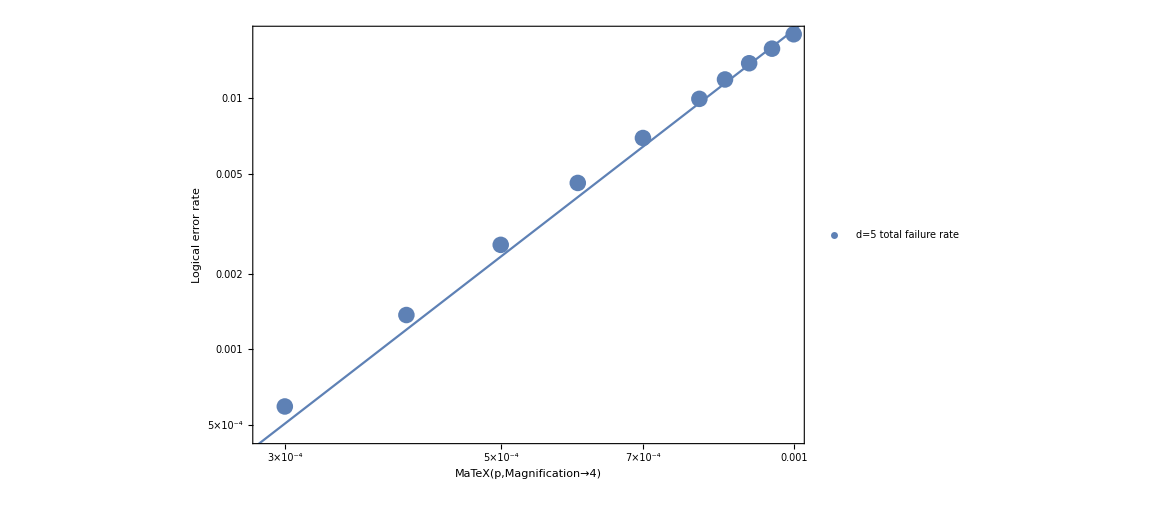

```mathematica
logicTot3Dd5LowReg={{0.0003,0.000591},{0.0004,0.001368},{0.0005,0.002605},{0.0006,0.004598},{0.0007,0.006945},{0.0008,0.009948},{0.00085,0.011886},{0.0009,0.013794},{0.00095,0.015768},{0.001,0.017996}};
nlmd5TotalLogColor=NonlinearModelFit[logicTot3Dd5LowReg,{a x^3},{a},x]
nlmd5TotalLogColor["EstimatedVariance"]
Show[ListLogLogPlot[{logicTot3Dd5LowReg},PlotLegends->Placed[{"d=5 total failure rate"},Scaled[{0.2,0.9}]],PlotMarkers->{Automatic,17}],LogLogPlot[nlmd5TotalLogColor[x],{x,0.0002,0.003},PlotRange->All],Frame->True,FrameLabel->{MaTeX[p,Magnification->4],Style["Logical error rate",Black,30]},FrameStyle->Directive[Black,20],ImageSize->{850,850}]
```

#### Distance 7

FittedModel[1.14099×10^10 x^4]

6.63101×10^-8

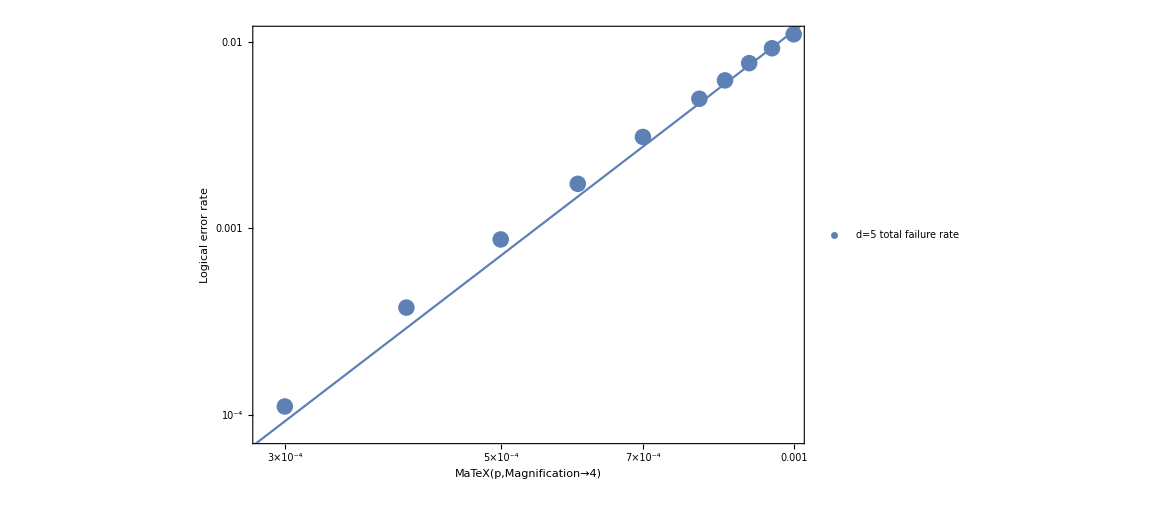

```mathematica
logicTot3Dd7LowReg={{0.0003,0.000111},{0.0004,0.000376},{0.0005,0.000872},{0.0006,0.001732},{0.0007,0.003089},{0.0008,0.004947},{0.00085,0.006208},{0.0009,0.007679},{0.00095,0.009227},{0.001,0.010965}};
nlmd7TotalLogColor=NonlinearModelFit[logicTot3Dd7LowReg,{a x^4},{a},x]
nlmd7TotalLogColor["EstimatedVariance"]
Show[ListLogLogPlot[{logicTot3Dd7LowReg},PlotLegends->Placed[{"d=5 total failure rate"},Scaled[{0.2,0.9}]],PlotMarkers->{Automatic,17}],LogLogPlot[nlmd7TotalLogColor[x],{x,0.0002,0.003},PlotRange->All],Frame->True,FrameLabel->{MaTeX[p,Magnification->4],Style["Logical error rate",Black,30]},FrameStyle->Directive[Black,20],ImageSize->{850,850}]
```

#### Distance 9

FittedModel[6.26365×10^12 x^5]

1.09612×10^-8

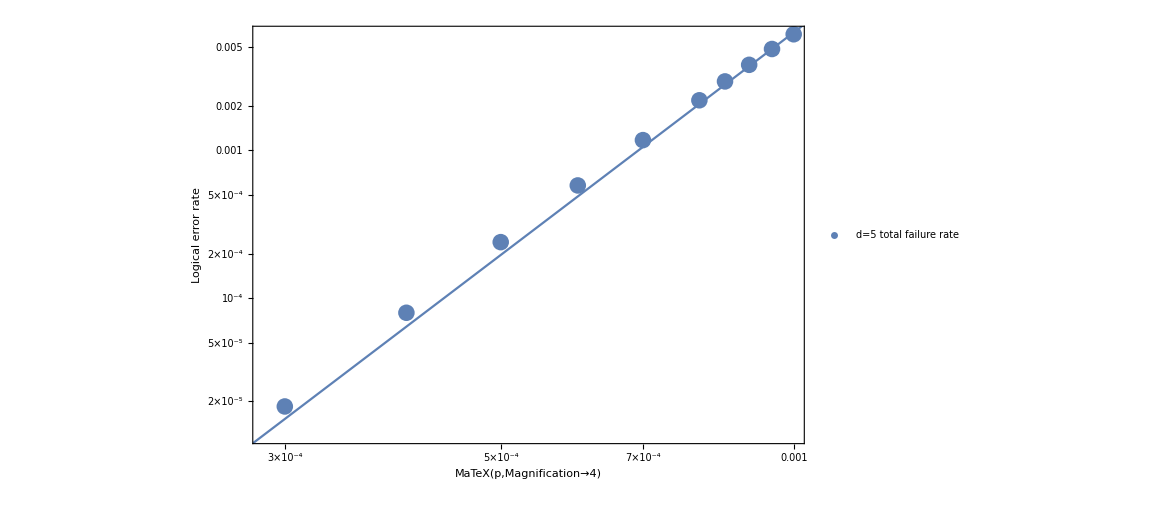

```mathematica
logicTot3Dd9LowReg={{0.0003,0.0000185},{0.0004,0.0000796},{0.0005,0.0002391},{0.0006,0.0005781},{0.0007,0.0011711},{0.0008,0.0021776},{0.00085,0.0029213},{0.0009,0.0037828},{0.00095,0.0048396},{0.001,0.0060869}};
nlmd9TotalLogColor=NonlinearModelFit[logicTot3Dd9LowReg,{a x^5},{a},x]
nlmd9TotalLogColor["EstimatedVariance"]
Show[ListLogLogPlot[{logicTot3Dd9LowReg},PlotLegends->Placed[{"d=5 total failure rate"},Scaled[{0.2,0.9}]],PlotMarkers->{Automatic,17}],LogLogPlot[nlmd9TotalLogColor[x],{x,0.0002,0.003},PlotRange->All],Frame->True,FrameLabel->{MaTeX[p,Magnification->4],Style["Logical error rate",Black,30]},FrameStyle->Directive[Black,20],ImageSize->{850,850}]
```

#### Distance 11

FittedModel[3.24088×10^15 x^6]

2.53985×10^-9

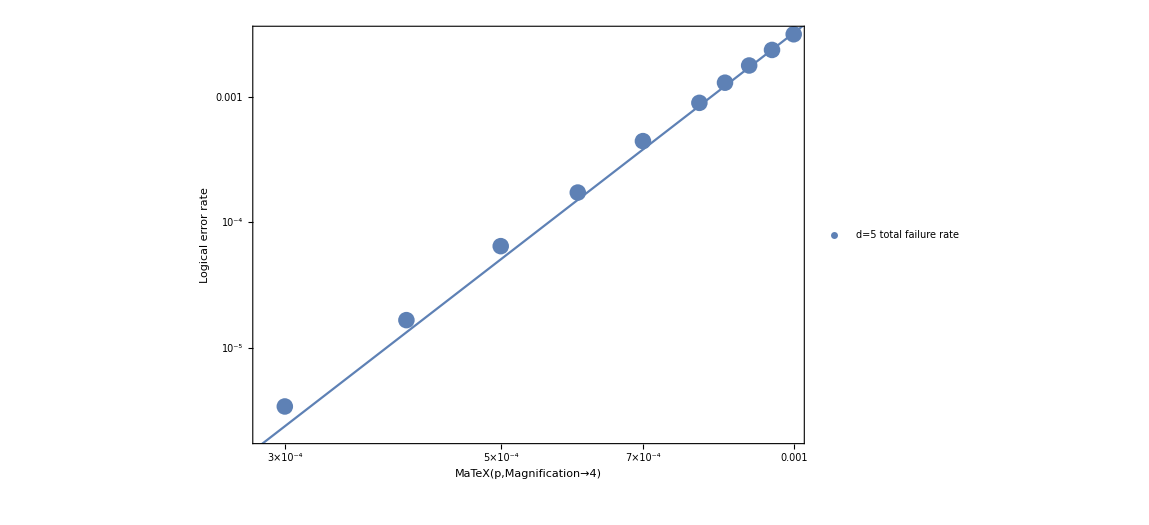

```mathematica
logicTot3Dd11LowReg={{0.0003,3.4*^-6},{0.0004,0.0000166},{0.0005,0.0000646},{0.0006,0.0001729},{0.0007,0.0004447},{0.0008,0.0008981},{0.00085,0.0013004},{0.0009,0.0017836},{0.00095,0.002373},{0.001,0.0031643}};
nlmd11TotalLogColor=NonlinearModelFit[logicTot3Dd11LowReg,{a x^6},{a},x]
nlmd11TotalLogColor["EstimatedVariance"]
Show[ListLogLogPlot[{logicTot3Dd11LowReg},PlotLegends->Placed[{"d=5 total failure rate"},Scaled[{0.2,0.9}]],PlotMarkers->{Automatic,17}],LogLogPlot[nlmd11TotalLogColor[x],{x,0.0002,0.003},PlotRange->All],Frame->True,FrameLabel->{MaTeX[p,Magnification->4],Style["Logical error rate",Black,30]},FrameStyle->Directive[Black,20],ImageSize->{850,850}]
```

#### Distance 13

FittedModel[9.79431×10^16 x^6.6]

6.90762×10^-12

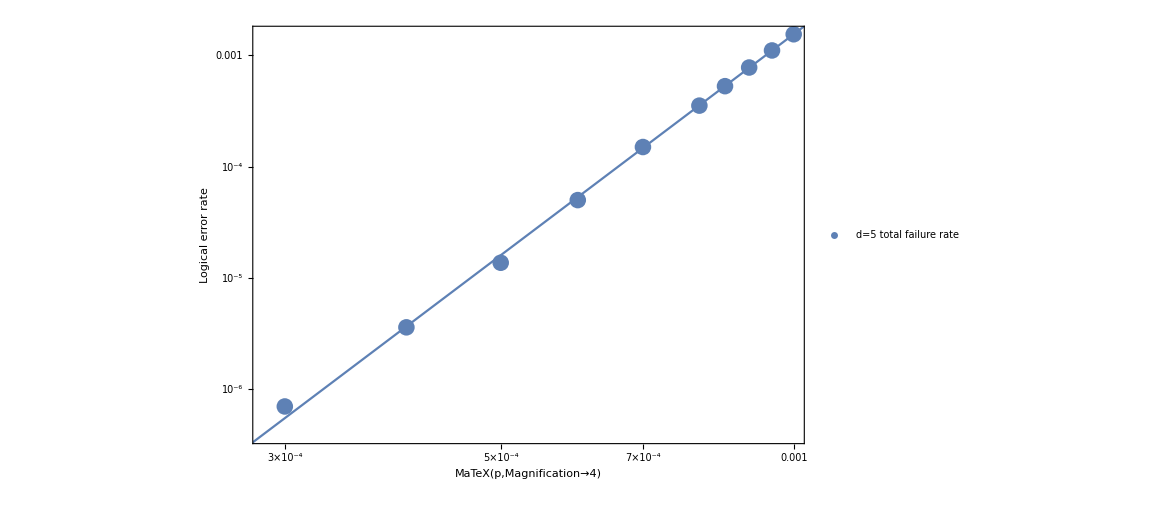

```mathematica
logicTot3Dd13LowReg={{0.0003,7.*^-7},{0.0004,3.6*^-6},{0.0005,0.0000137},{0.0006,0.0000501},{0.0007,0.0001503},{0.0008,0.000354},{0.00085,0.0005294},{0.0009,0.0007789},{0.00095,0.0011085},{0.001,0.0015495}};
nlmd13TotalLogColor=NonlinearModelFit[logicTot3Dd13LowReg,{a x^6.6},{a},x]
nlmd13TotalLogColor["EstimatedVariance"]
Show[ListLogLogPlot[{logicTot3Dd13LowReg},PlotLegends->Placed[{"d=5 total failure rate"},Scaled[{0.2,0.9}]],PlotMarkers->{Automatic,17}],LogLogPlot[nlmd13TotalLogColor[x],{x,0.0002,0.003},PlotRange->All],Frame->True,FrameLabel->{MaTeX[p,Magnification->4],Style["Logical error rate",Black,30]},FrameStyle->Directive[Black,20],ImageSize->{850,850}]
```

#### Distance 15

FittedModel[2.56637×10^18 x^7.2]

3.81402×10^-6

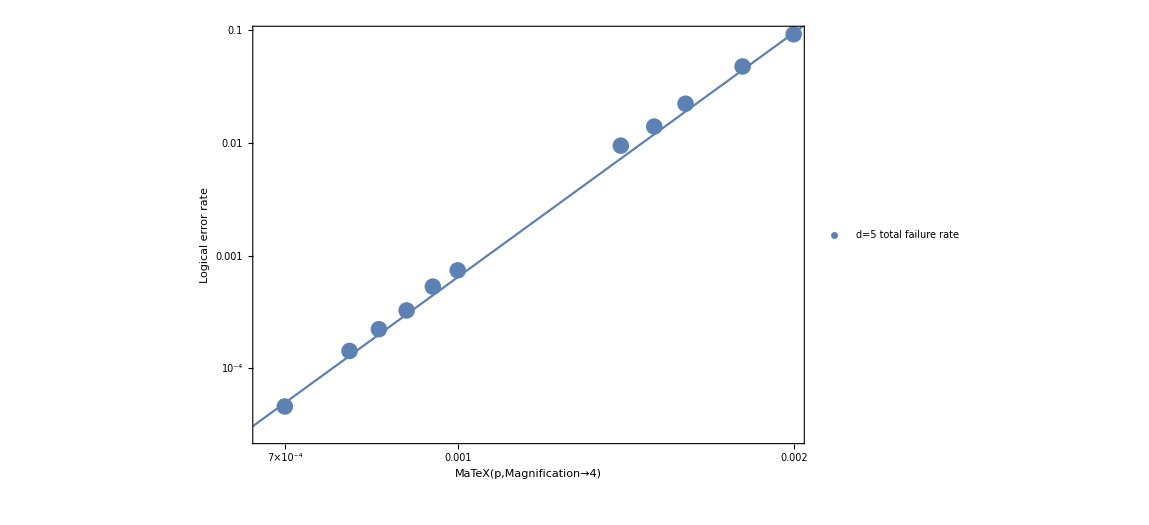

```mathematica
logicTot3Dd15LowReg={{0.0007,0.000046},{0.0008,0.000143},{0.00085,0.000223},{0.0009,0.000327},{0.00095,0.000532},{0.001,0.000742},{0.0014,0.00947},{0.0015,0.01399},{0.0016,0.02231},{0.0018,0.04773},{0.002,0.09213}};
nlmd15TotalLogColor=NonlinearModelFit[logicTot3Dd15LowReg,{a x^7.2},{a},x]
nlmd15TotalLogColor["EstimatedVariance"]
Show[ListLogLogPlot[{logicTot3Dd15LowReg},PlotLegends->Placed[{"d=5 total failure rate"},Scaled[{0.2,0.9}]],PlotMarkers->{Automatic,17}],LogLogPlot[nlmd15TotalLogColor[x],{x,0.0002,0.003},PlotRange->All],Frame->True,FrameLabel->{MaTeX[p,Magnification->4],Style["Logical error rate",Black,30]},FrameStyle->Directive[Black,20],ImageSize->{850,850}]
```

```mathematica
nlmd13TotalLogColor[5*10^-4]
```

0.0000160021

#### All curves plotted

```mathematica
TotalNumQubitsCKcolor[19]
```

784

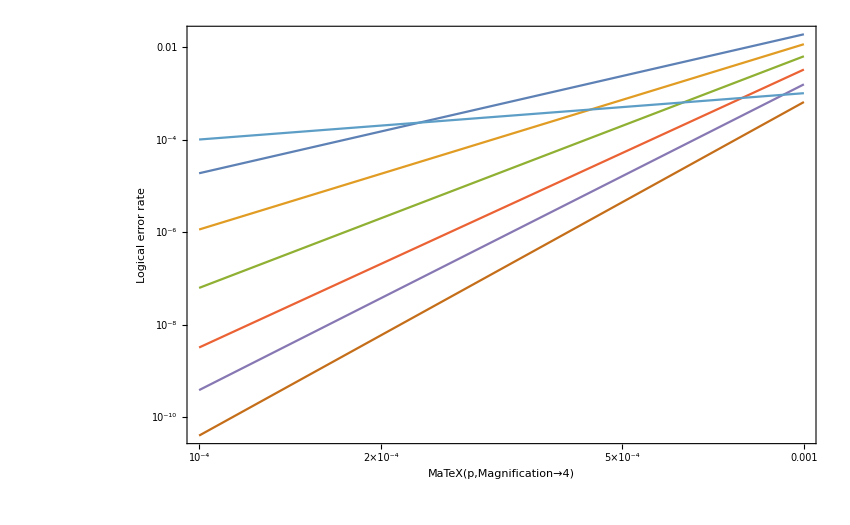

```mathematica
Show[LogLogPlot[{nlmd5TotalLogColor[x],nlmd7TotalLogColor[x],nlmd9TotalLogColor[x],nlmd11TotalLogColor[x],nlmd13TotalLogColor[x],nlmd15TotalLogColor[x],x},{x,0.0001,0.001},PlotRange->All],Frame->True,FrameLabel->{MaTeX[p,Magnification->4],Style["Logical error rate",Black,30]},FrameStyle->Directive[Black,20],ImageSize->{850,850}]
```

## Magic state prep logical failure rate and overhead

```mathematica
SimpleColorQubit[d_]:=(3*d-1)^2/4;
```

```mathematica
numWeight4Stabs=3/2*(d-1);
numWeight6Stabs=(3*d^2-12*d+9)/8;
numQubits[d_]:=(3*d^2+1)/4;
TotNumQubitsMagicState[d_]:=(6*d^2-9*d+5)/2;
```

```mathematica
numQubitsd3=16;
numQubitsd5=55;
numQubitsd7=118;
(*Surface code qubit number*)
surfaceQUbit[d_]:=2*d^2-1;
(*Number of time steps for one Hadamard measurement circuit*)
tHd3=8;
tHd5=13;
tHd7=17;
tECd3=14;
tECd5=18;
tGrowingPhysical=14;
```

### Growing scheme acceptance probability

#### Physical to d=3

```mathematica
GrowProbAcceptd3Physical={{10^-4,0.9897},{2*10^-4,0.9800},{3*10^-4,0.9701},{4*10^-4,0.9601},{5*10^-4,0.9491},{6*10^-4,0.9420},{7*10^-4,0.9312},{8*10^-4,0.9209},{9*10^-4,0.9137},{10^-3,0.9028}};
```

#### Physical to d=5

```mathematica
GrowProbAcceptd5Physical={{10^-4,0.9711},{2*10^-4,0.9441},{3*10^-4,0.9159},{4*10^-4,0.8895},{5*10^-4,0.8648},{6*10^-4,0.8438},{7*10^-4,0.8198},{8*10^-4,0.7944},{9*10^-4,0.7722},{10^-3,0.7471}};
```

#### Physical to d=7

```mathematica
GrowProbAcceptd7Physical={{10^-4,0.9462},{2*10^-4,0.8948},{3*10^-4,0.8500},{4*10^-4,0.8014},{5*10^-4,0.7574},{6*10^-4,0.7209},{7*10^-4,0.6796},{8*10^-4,0.6447},{9*10^-4,0.6098},{10^-3,0.5757}};
```

### Physical to logical d=3

#### Logical error rates

FittedModel[63.2235 x^2]

8.80363×10^-14

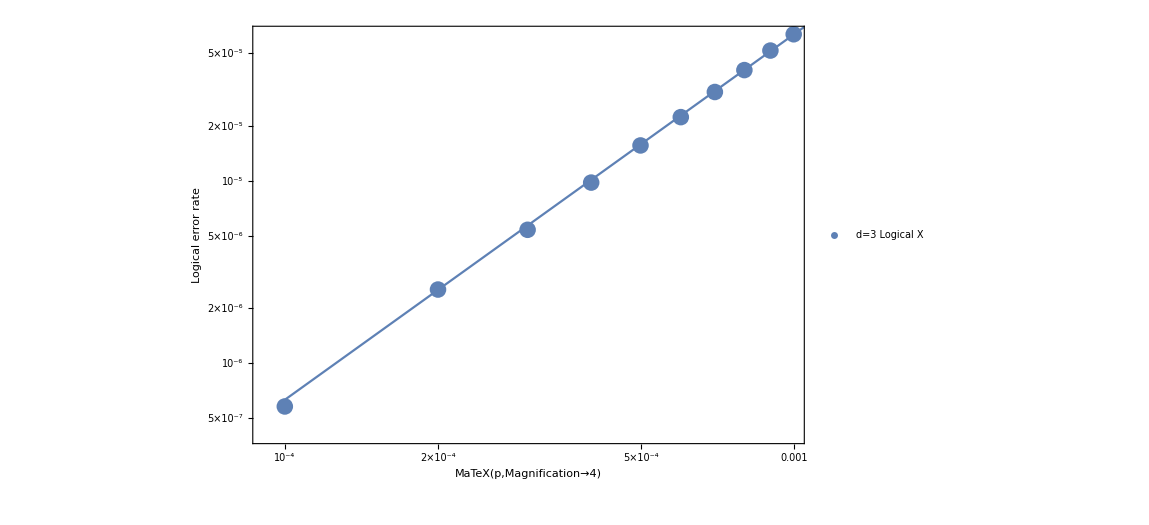

```mathematica
datad3PhysicToLogX={{0.0001,5.81411*10^-7},{0.0002,2.53873*10^-6},{0.0003,5.39125*10^-6},{0.0004,9.77572*10^-6},{0.0005,1.56136*10^-5},{0.0006,2.23106*10^-5},{0.0007,3.0628*10^-5},{0.0008,4.03682*10^-5},{0.0009,5.16356*10^-5},{0.001,6.34039*10^-5}};
nlmd3MagicPrepLogX=NonlinearModelFit[ datad3PhysicToLogX,{a x^2},{a},x]
nlmd3MagicPrepLogX["EstimatedVariance"]
Show[ListLogLogPlot[{datad3PhysicToLogX},PlotLegends->Placed[{"d=3 Logical X"},Scaled[{0.2,0.9}]],PlotMarkers->{Automatic,17}],LogLogPlot[nlmd3MagicPrepLogX[x],{x,0.0001,0.003},PlotRange->All],Frame->True,FrameLabel->{MaTeX[p,Magnification->4],Style["Logical error rate",Black,30]},FrameStyle->Directive[Black,20],ImageSize->{850,850}]
```

FittedModel[279.043 x^2]

2.92707×10^-12

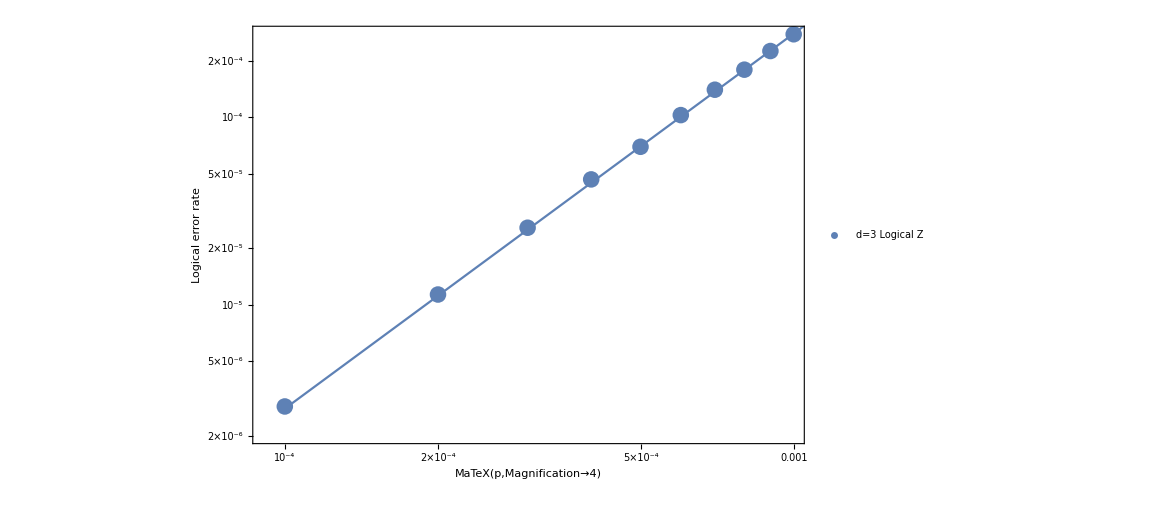

```mathematica
datad3PhysicToLogZ={{0.0001,2.86625*10^-6},{0.0002,1.13307*10^-5},{0.0003,2.57252*10^-5},{0.0004,4.65727*10^-5},{0.0005,6.95102*10^-5},{0.0006,0.000102554},{0.0007,0.000140056},{0.0008,0.000179143},{0.0009,0.000225224},{0.001,0.000276644}};
nlmd3MagicPrepLogZ=NonlinearModelFit[ datad3PhysicToLogZ,{a x^2},{a},x]
nlmd3MagicPrepLogZ["EstimatedVariance"]
Show[ListLogLogPlot[{datad3PhysicToLogZ},PlotLegends->Placed[{"d=3 Logical Z"},Scaled[{0.2,0.9}]],PlotMarkers->{Automatic,17}],LogLogPlot[nlmd3MagicPrepLogZ[x],{x,0.0001,0.003},PlotRange->All],Frame->True,FrameLabel->{MaTeX[p,Magnification->4],Style["Logical error rate",Black,30]},FrameStyle->Directive[Black,20],ImageSize->{850,850}]
```

```mathematica
TotalLogErrRateMagicStated3={};
Do[TotalLogErrRateMagicStated3=Append[TotalLogErrRateMagicStated3,{datad3PhysicToLogZ[[i,1]],datad3PhysicToLogZ[[i,2]]+datad3PhysicToLogX[[i,2]]}],{i,1,10}];
nlmd3MagicPrepLogTotal=NonlinearModelFit[ TotalLogErrRateMagicStated3,{a x^2},{a},x]
```

FittedModel[342.267 x^2]

#### Acceptance probability

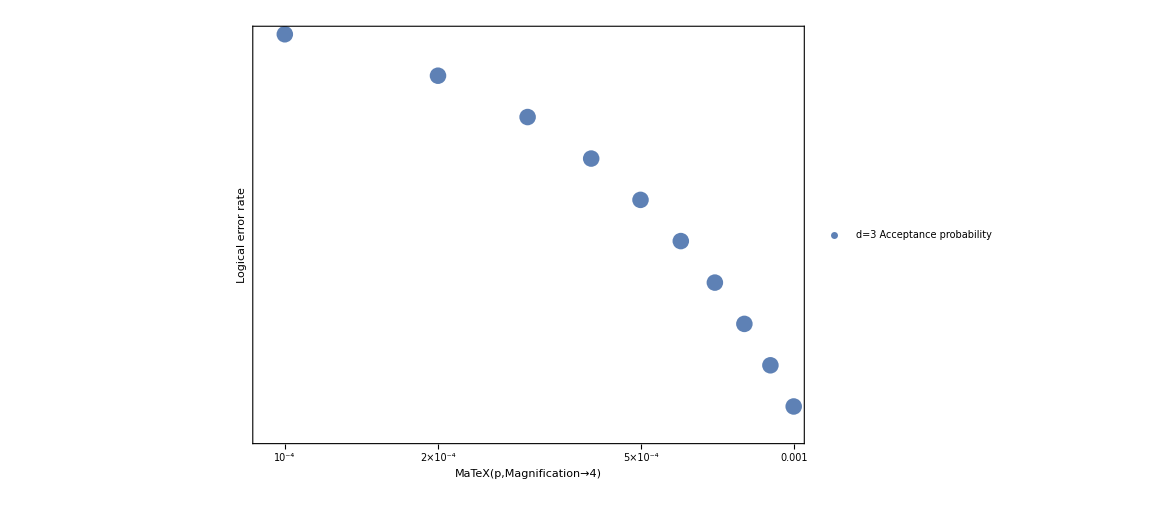

```mathematica
P2CurveD3PhysToLog={{0.0001,0.980374},{0.0002,0.96111},{0.0003,0.942268},{0.0004,0.923718},{0.0005,0.905623},{0.0006,0.88792},{0.0007,0.87044},{0.0008,0.853394},{0.0009,0.836633},{0.001,0.820297}};
Show[ListLogLogPlot[{P2CurveD3PhysToLog},PlotLegends->Placed[{"d=3 Acceptance probability"},Scaled[{0.8,0.9}]],PlotMarkers->{Automatic,17}],Frame->True,FrameLabel->{MaTeX[p,Magnification->4],Style["Logical error rate",Black,30]},FrameStyle->Directive[Black,20],ImageSize->{850,850}]
```

#### Total acceptance probability

```mathematica
P2CurveD3PhysToLogTotal={};
Do[P2CurveD3PhysToLogTotal=Append[P2CurveD3PhysToLogTotal,{P2CurveD3PhysToLog[[i,1]],P2CurveD3PhysToLog[[i,2]]*GrowProbAcceptd3Physical[[i,2]]}],{i,1,10}];
```

```mathematica
Show[ListLogLogPlot[{P2CurveD3PhysToLog},PlotLegends->Placed[{"d=3 Acceptance probability"},Scaled[{0.8,0.9}]],PlotMarkers->{Automatic,17}],Frame->True,FrameLabel->{MaTeX[p,Magnification->4],Style["Logical error rate",Black,30]},FrameStyle->Directive[Black,20],ImageSize->{850,850}]
```

-Graphics-

#### Qubit overhead

```mathematica
QubitOverheadd3Physical={};
Do[QubitOverheadd3Physical=Append[QubitOverheadd3Physical,{TotalLogErrRateMagicStated3[[i,2]],TotNumQubitsMagicState[3]/P2CurveD3PhysToLogTotal[[i,2]]}],{i,1,10}]
```

```mathematica
QubitOverheadd3Physical
```

{{3.44766×10^-6,16.4902},{0.0000138694,16.9872},{0.0000311165,17.5037},{0.0000563484,18.0411},{0.0000851238,18.6149},{0.000124865,19.1291},{0.000170684,19.7396},{0.000219511,20.3591},{0.00027686,20.9306},{0.000340048,21.6052}}

#### Space-time overhead

```mathematica
tT=tGrowingPhysical+tHd3+tECd3;
SpaceTimeOverheadd3Physical={};
Do[SpaceTimeOverheadd3Physical=Append[SpaceTimeOverheadd3Physical,{TotalLogErrRateMagicStated3[[i,2]],QubitOverheadd3Physical[[i,2]]*tT}],{i,1,10}];
SpaceTimeOverheadd3Physical
```

{{3.44766×10^-6,593.645},{0.0000138694,611.538},{0.0000311165,630.132},{0.0000563484,649.481},{0.0000851238,670.136},{0.000124865,688.649},{0.000170684,710.625},{0.000219511,732.927},{0.00027686,753.501},{0.000340048,777.785}}

### Physical to logical d=5

#### Logical error rates

FittedModel[4086.38 x^3]

3.04464×10^-14

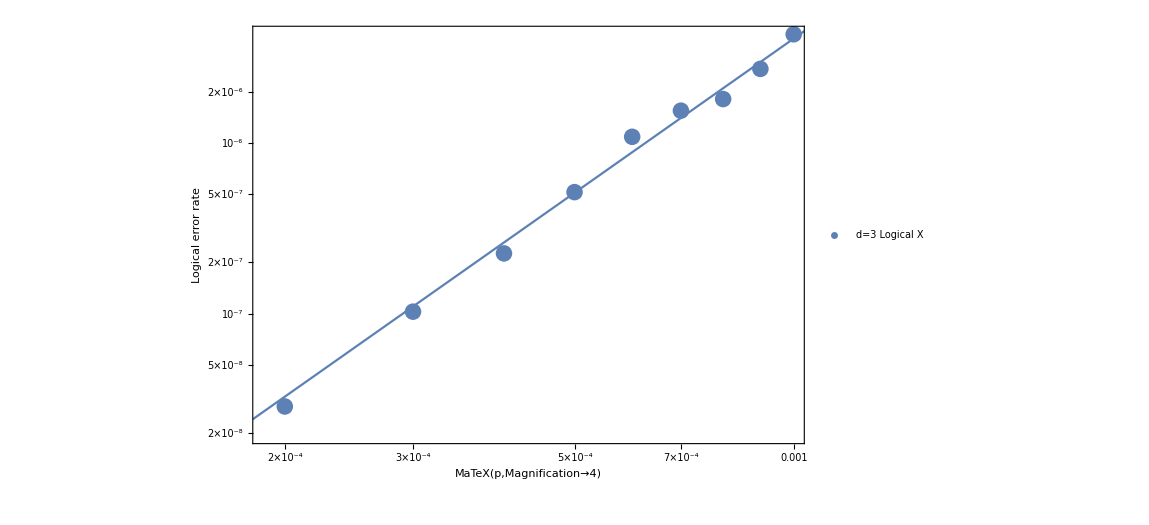

```mathematica
datad5PhysicToLogX={{0.0001,0},{0.0002,2.86522*10^-8},{0.0003,1.02875*10^-7},{0.0004,2.2568*10^-7},{0.0005,5.15544*10^-7},{0.0006,1.08711*10^-6},{0.0007,1.54634*10^-6},{0.0008,1.80833*10^-6},{0.0009,2.716*10^-6},{0.001,4.33159*10^-6}};
nlmd5MagicPrepLogX=NonlinearModelFit[ datad5PhysicToLogX,{a x^3},{a},x]
nlmd5MagicPrepLogX["EstimatedVariance"]
Show[ListLogLogPlot[{datad5PhysicToLogX},PlotLegends->Placed[{"d=3 Logical X"},Scaled[{0.2,0.9}]],PlotMarkers->{Automatic,17}],LogLogPlot[nlmd5MagicPrepLogX[x],{x,0.0001,0.003},PlotRange->All],Frame->True,FrameLabel->{MaTeX[p,Magnification->4],Style["Logical error rate",Black,30]},FrameStyle->Directive[Black,20],ImageSize->{850,850}]
```

FittedModel[40878.5 x^3]

8.00869×10^-13

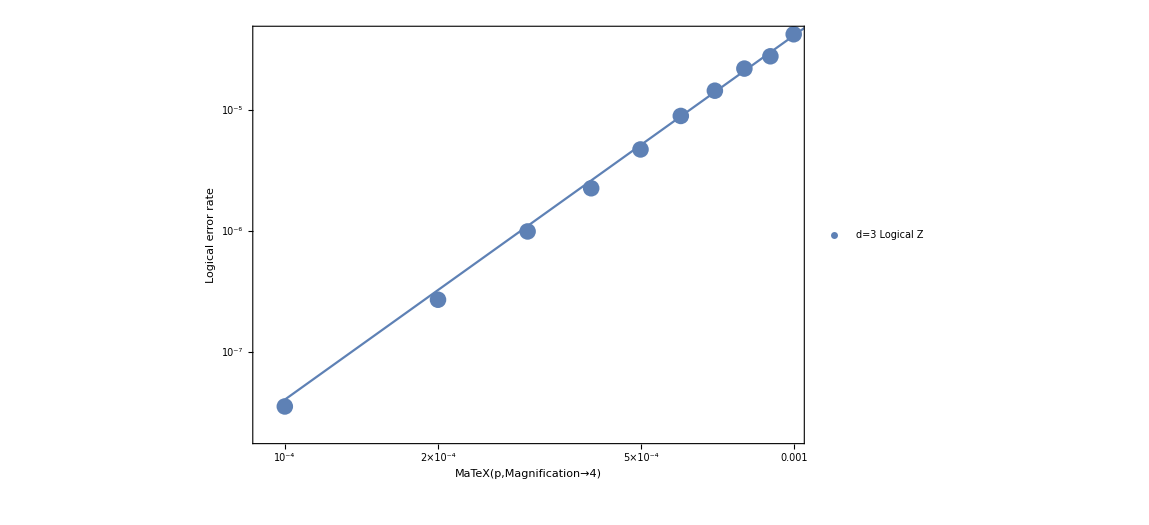

```mathematica
datad5PhysicToLogZ={{0.0001,3.59081*10^-8},{0.0002,2.72196*10^-7},{0.0003,9.94454*10^-7},{0.0004,2.2568*10^-6},{0.0005,4.71355*10^-6},{0.0006,8.90252*10^-6},{0.0007,1.43739*10^-5},{0.0008,2.18682*10^-5},{0.0009,2.76127*10^-5},{0.001,4.19322*10^-5}};
nlmd5MagicPrepLogZ=NonlinearModelFit[ datad5PhysicToLogZ,{a x^3},{a},x]
nlmd5MagicPrepLogZ["EstimatedVariance"]
Show[ListLogLogPlot[{datad5PhysicToLogZ},PlotLegends->Placed[{"d=3 Logical Z"},Scaled[{0.2,0.9}]],PlotMarkers->{Automatic,17}],LogLogPlot[nlmd5MagicPrepLogZ[x],{x,0.0001,0.003},PlotRange->All],Frame->True,FrameLabel->{MaTeX[p,Magnification->4],Style["Logical error rate",Black,30]},FrameStyle->Directive[Black,20],ImageSize->{850,850}]
```

```mathematica
TotalLogErrRateMagicStated5={};
Do[TotalLogErrRateMagicStated5=Append[TotalLogErrRateMagicStated5,{datad5PhysicToLogZ[[i,1]],datad5PhysicToLogZ[[i,2]]+datad5PhysicToLogX[[i,2]]}],{i,1,10}];
nlmd5MagicPrepLogTotal=NonlinearModelFit[ TotalLogErrRateMagicStated5,{a x^3},{a},x]
```

FittedModel[44964.9 x^3]

```mathematica
TotalLogErrRateMagicStated5
```

{{0.0001,3.59081×10^-8},{0.0002,3.00848×10^-7},{0.0003,1.09733×10^-6},{0.0004,2.48248×10^-6},{0.0005,5.22909×10^-6},{0.0006,9.98963×10^-6},{0.0007,0.0000159202},{0.0008,0.0000236765},{0.0009,0.0000303287},{0.001,0.0000462638}}

#### Acceptance probability

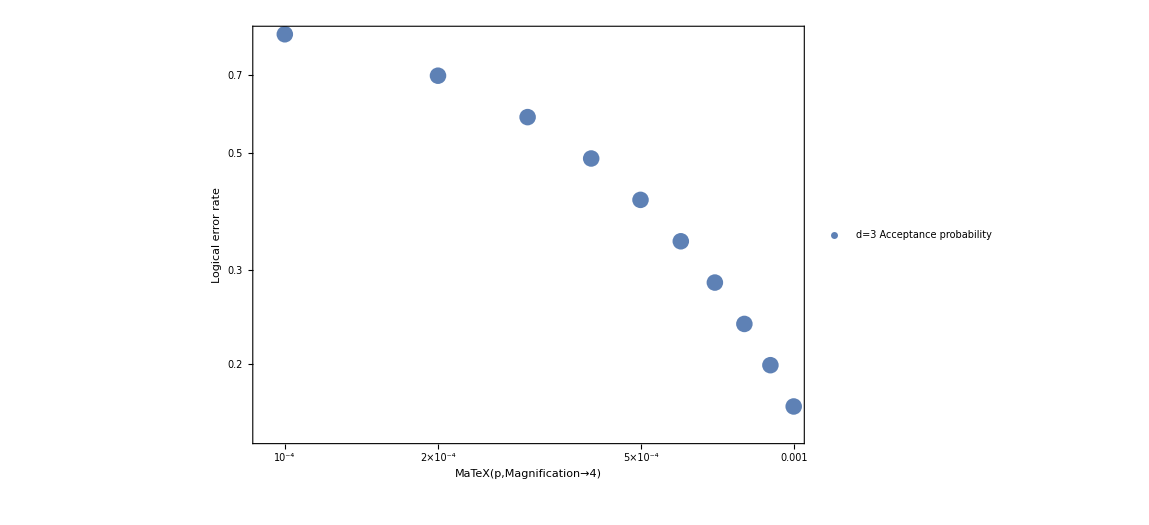

```mathematica
P2CurveD5PhysToLog={{0.0001,0.835465},{0.0002,0.698028},{0.0003,0.583235},{0.0004,0.487416},{0.0005,0.407337},{0.0006,0.340353},{0.0007,0.284543},{0.0008,0.237788},{0.0009,0.198822},{0.001,0.166221}};
Show[ListLogLogPlot[{P2CurveD5PhysToLog},PlotLegends->Placed[{"d=3 Acceptance probability"},Scaled[{0.8,0.9}]],PlotMarkers->{Automatic,17}],Frame->True,FrameLabel->{MaTeX[p,Magnification->4],Style["Logical error rate",Black,30]},FrameStyle->Directive[Black,20],ImageSize->{850,850}]
```

#### Total acceptance probability

```mathematica
P2CurveD5PhysToLogTotal={};
Do[P2CurveD5PhysToLogTotal=Append[P2CurveD5PhysToLogTotal,{P2CurveD5PhysToLog[[i,1]],P2CurveD5PhysToLog[[i,2]]*GrowProbAcceptd5Physical[[i,2]]}],{i,1,10}]
```

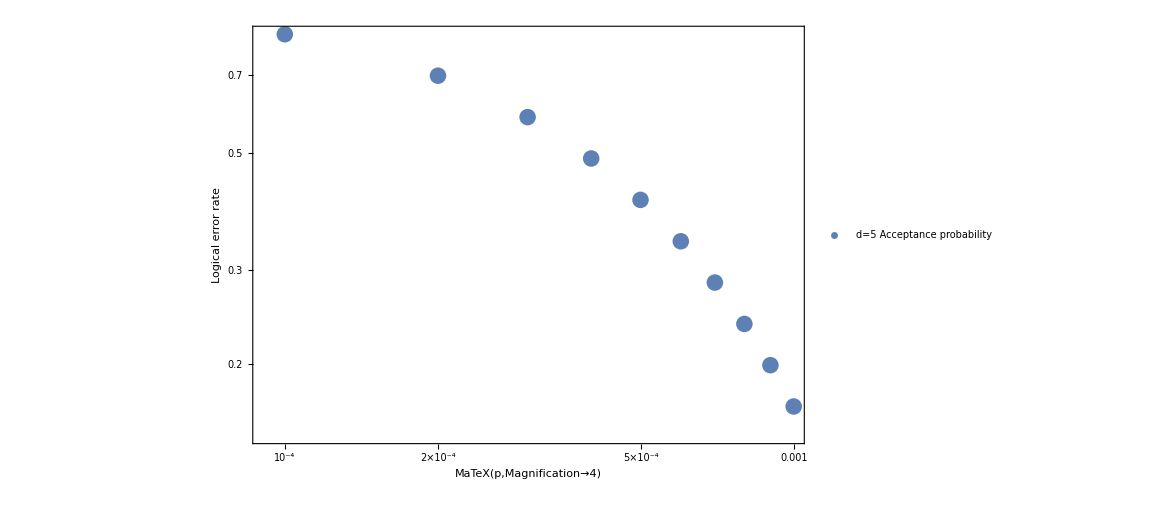

```mathematica
Show[ListLogLogPlot[{P2CurveD5PhysToLog},PlotLegends->Placed[{"d=5 Acceptance probability"},Scaled[{0.8,0.9}]],PlotMarkers->{Automatic,17}],Frame->True,FrameLabel->{MaTeX[p,Magnification->4],Style["Logical error rate",Black,30]},FrameStyle->Directive[Black,20],ImageSize->{850,850}]
```

#### Qubit overhead

```mathematica
QubitOverheadd5Physical={};
Do[QubitOverheadd5Physical=Append[QubitOverheadd5Physical,{TotalLogErrRateMagicStated5[[i,2]],TotNumQubitsMagicState[5]/P2CurveD5PhysToLogTotal[[i,2]]}],{i,1,10}]
```

```mathematica
QubitOverheadd5Physical
```

{{3.59081×10^-8,67.7908},{3.00848×10^-7,83.4587},{1.09733×10^-6,102.961},{2.48248×10^-6,126.858},{5.22909×10^-6,156.132},{9.98963×10^-6,191.511},{0.0000159202,235.78},{0.0000236765,291.161},{0.0000303287,358.235},{0.0000462638,442.892}}

#### Space-time overhead

```mathematica
tT=tGrowingPhysical+2*tHd5+2*tECd5;
SpaceTimeOverheadd5Physical={};
Do[SpaceTimeOverheadd5Physical=Append[SpaceTimeOverheadd5Physical,{TotalLogErrRateMagicStated5[[i,2]],QubitOverheadd5Physical[[i,2]]*tT}],{i,1,10}];
SpaceTimeOverheadd5Physical
```

{{3.59081×10^-8,5152.1},{3.00848×10^-7,6342.86},{1.09733×10^-6,7825.01},{2.48248×10^-6,9641.19},{5.22909×10^-6,11866.1},{9.98963×10^-6,14554.8},{0.0000159202,17919.3},{0.0000236765,22128.3},{0.0000303287,27225.9},{0.0000462638,33659.8}}

```mathematica
{0.00004626379,33659.80956998168}
```

### Physical to logical d=7

#### Logical error rates

FittedModel[4.89564×10^6 x^4]

2.07831×10^-17

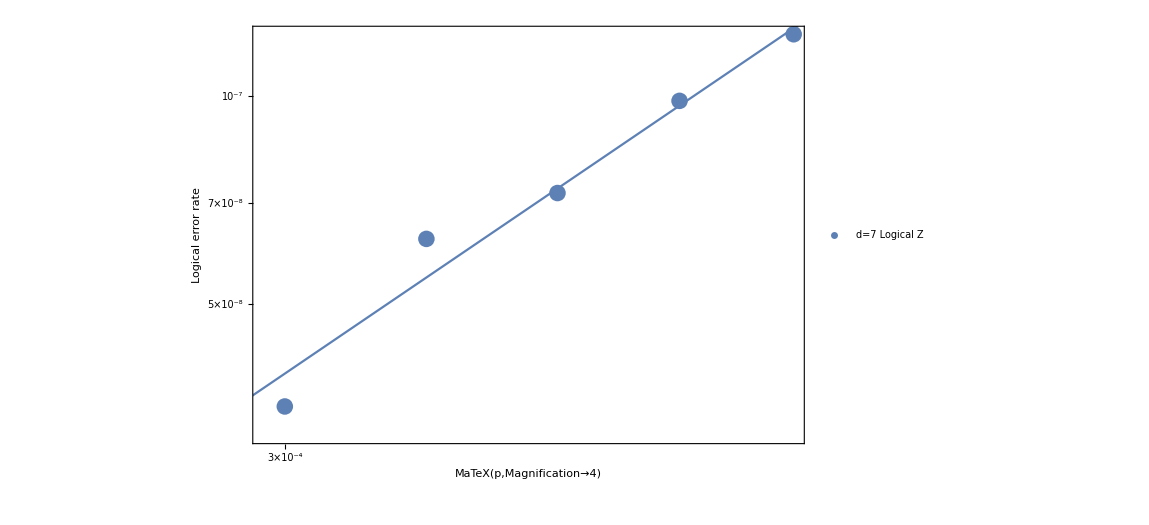

```mathematica
datad7PhysicToLogZ={{0.0003,3.5545*10^-8},{0.000325,6.21151*10^-8},{0.00035,7.23637*10^-8},{0.000375,9.83764*10^-8},{0.0004,1.228*10^-7}};
nlmd7MagicPrepLogZ=NonlinearModelFit[ datad7PhysicToLogZ,{a x^4},{a},x]
nlmd7MagicPrepLogZ["EstimatedVariance"]
Show[ListLogLogPlot[{datad7PhysicToLogZ},PlotLegends->Placed[{"d=7 Logical Z"},Scaled[{0.2,0.9}]],PlotMarkers->{Automatic,17}],LogLogPlot[nlmd7MagicPrepLogZ[x],{x,0.0002,0.003},PlotRange->All],Frame->True,FrameLabel->{MaTeX[p,Magnification->4],Style["Logical error rate",Black,30]},FrameStyle->Directive[Black,20],ImageSize->{850,850}]
```

#### Acceptance probability

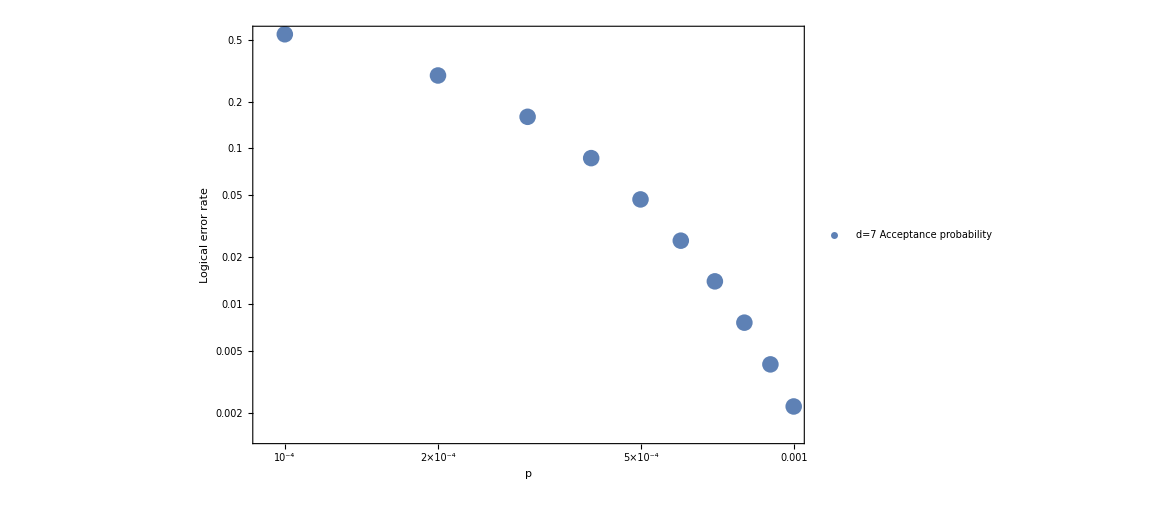

```mathematica
P2CurveD7PhysToLog={{0.0001,0.5410},{0.0002,0.2941},{0.0003,0.159614},{0.0004,0.0866269},{0.0005,0.047034},{0.0006,0.0255501},{0.0007,0.0140},{0.0008,0.0076},{0.0009,0.0041},{0.001,0.0022}};
Show[ListLogLogPlot[{P2CurveD7PhysToLog},PlotLegends->Placed[{"d=7 Acceptance probability"},Scaled[{0.8,0.9}]],PlotMarkers->{Automatic,17}],Frame->True,FrameLabel->{p,Style["Logical error rate",Black,30]},FrameStyle->Directive[Black,20],ImageSize->{850,850}]
```

#### Total acceptance probability

```mathematica
P2CurveD7PhysToLogTotal={};
Do[P2CurveD7PhysToLogTotal=Append[P2CurveD7PhysToLogTotal,{P2CurveD7PhysToLog[[i,1]],P2CurveD7PhysToLog[[i,2]]*GrowProbAcceptd7Physical[[i,2]]}],{i,1,10}]
```

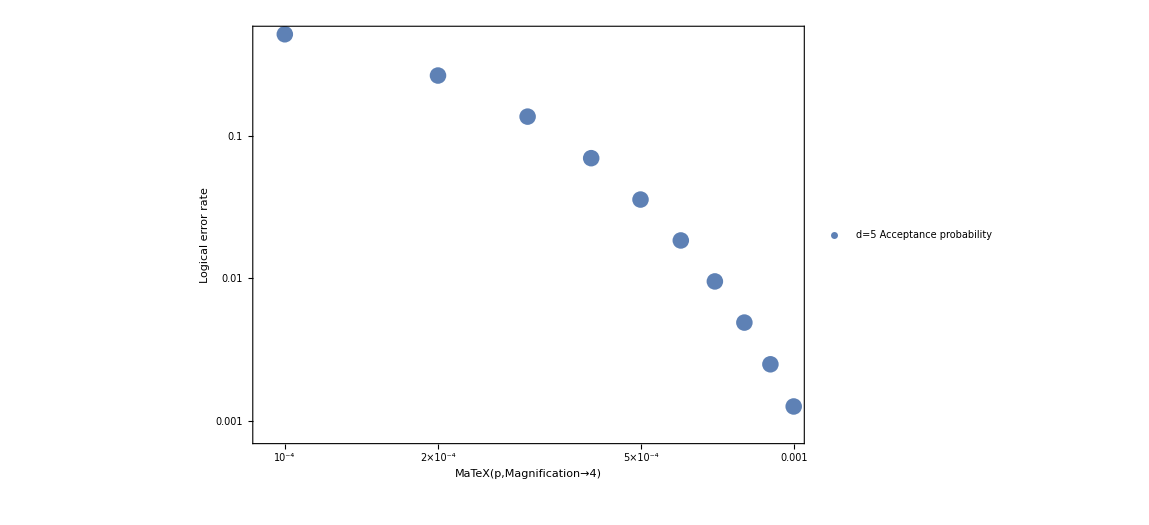

```mathematica
Show[ListLogLogPlot[{P2CurveD7PhysToLogTotal},PlotLegends->Placed[{"d=5 Acceptance probability"},Scaled[{0.8,0.9}]],PlotMarkers->{Automatic,17}],Frame->True,FrameLabel->{MaTeX[p,Magnification->4],Style["Logical error rate",Black,30]},FrameStyle->Directive[Black,20],ImageSize->{850,850}]
```

#### Qubit overhead

```mathematica
QubitOverheadd7Physical={};
Do[QubitOverheadd7Physical=Append[QubitOverheadd7Physical,{nlmd7MagicPrepLogZ[i*10^-4],TotNumQubitsMagicState[7]/P2CurveD7PhysToLogTotal[[i,2]]}],{i,1,10}]
```

#### Space-time overhead

```mathematica
tT=tGrowingPhysical+3*tHd5+3*tECd5;
SpaceTimeOverheadd7Physical={};
Do[SpaceTimeOverheadd7Physical=Append[SpaceTimeOverheadd7Physical,{QubitOverheadd7Physical[[i,2]],QubitOverheadd7Physical[[i,2]]*tT}],{i,1,10}];
SpaceTimeOverheadd7Physical
```

{{230.516,24665.3},{448.395,47978.3},{869.745,93062.7},{1699.73,181871.},{3312.42,354428.},{6406.4,685485.},{12402.3,1.32704×10^6},{24083.,2.57688×10^6},{47196.6,5.05004×10^6},{93167.2,9.96889×10^6}}

```mathematica
nlmd7MagicPrepLogZ[10^-3]
```

4.89564×10^-6

## Magic state prep logical failure rate (Logical Clifford gates encoded in the Color code)

```mathematica
(*Physical |H> state prep polynomials*)
pLdist3[p_]:=342*p^2;
pLd5[p_]:=44964*p^3;
pLd7[p_]:=3.16824651*10^6*p^4;
(*Color code logical error rate polynomials*)
pLcolorCoded5[p_]:=1.869169911951*10^7* p^3;
pLcolorCoded7[p_]:=1.14099418669480*10^10* p^4;
pLcolorCoded9[p_]:=6.263653380559652*10^12* p^5;
pLcolorCoded11[p_]:=3.2408754697234595*10^15* p^6;
pLcolorCoded13[p_]:=9.794312581413016*10^16* p^6.6;
pLcolorCoded15[p_]:=2.566369337434091*10^18* p^7.2;
(*For each magic state prep scheme (Subscript[d, f] \in {3,5,7}, we give the required color code distance to achieve the desired logical failure rate*)
SimpleColorQubit[d_]:=(3*d-1)^2/4;
numQubits[d_]:=(3*d^2+1)/4;
TotNumQubitsMagicState[d_]:=(6*d^2-9*d+5)/2;
(*Number of time steps for one Hadamard measurement circuit*)
tHd3=8;
tHd5=13;
tHd7=17;
tECd3=14;
tECd5=18;
tGrowingPhysical=14;
nMaxd3=16;
nMaxd5=55;
nMaxd7=118;
```

### Target logical failure rate 10^-8

#### d_f=3 Magic State

```mathematica
(*p=10^-4*)
pLdist3[pLcolorCoded7[10^-4]]
(*p=2*10^-4*)
pLdist3[pLcolorCoded9[2*10^-4]]
(*p=3*10^-4*)
pLdist3[pLcolorCoded11[3*10^-4]]
(*p=4*10^-4*)
pLdist3[pLcolorCoded13[4*10^-4]]
(*p=5*10^-4*)
pLdist3[pLcolorCoded15[5*10^-4]]
```

4.45239×10^-10

1.37398×10^-9

1.909×10^-9

4.60432×10^-9

6.57404×10^-9

#### d_f=5 Magic State

```mathematica
(*p=10^-4*)
N[pLd5[10^-4]]
(*p=2*10^-4*)
pLd5[pLcolorCoded7[2*10^-4]]
(*p=3*10^-4*)
pLd5[pLcolorCoded7[3*10^-4]]
(*p=4*10^-4*)
pLd5[pLcolorCoded9[4*10^-4]]
(*p=5*10^-4*)
pLd5[pLcolorCoded11[5*10^-4]]
```

4.4964×10^-8

2.73574×10^-10

3.54953×10^-8

1.18645×10^-8

5.83864×10^-9

#### d_f=7 Magic State

```mathematica
(*p=10^-4*)
N[pLd7[10^-4]]
(*p=2*10^-4*)
pLd7[2*10^-4]
(*p=3*10^-4*)
pLd7[3*10^-4]
(*p=4*10^-4*)
pLd7[pLcolorCoded7[4*10^-4]]
(*p=5*10^-4*)
pLd7[pLcolorCoded9[5*10^-4]]
```

3.16825×10^-10

5.06919×10^-9

2.56628×10^-8

2.30628×10^-8

4.65082×10^-9

### Target logical failure rate 10^-10

#### d_f=3 Magic State

```mathematica
(*p=10^-4*)
pLdist3[pLcolorCoded7[10^-4]]
(*p=2*10^-4*)
pLdist3[pLcolorCoded11[2*10^-4]]
(*p=3*10^-4*)
pLdist3[pLcolorCoded13[3*10^-4]]
(*p=4*10^-4*)
pLdist3[pLcolorCoded15[4*10^-4]]
(*p=5*10^-4*)
(*Requires d=17 color code*)
pLdist3[pLcolorCoded15[5*10^-4]]
```

4.45239×10^-10

1.47133×10^-11

1.0327×10^-10

2.64441×10^-10

6.57404×10^-9

#### d_f=5 Magic State

```mathematica
(*p=10^-4*)
pLd5[pLcolorCoded5[10^-4]]
(*p=2*10^-4*)
pLd5[pLcolorCoded7[2*10^-4]]
(*p=3*10^-4*)
pLd5[pLcolorCoded9[3*10^-4]]
(*p=4*10^-4*)
pLd5[pLcolorCoded11[4*10^-4]]
(*p=5*10^-4*)
pLd5[pLcolorCoded13[5*10^-4]]
```

2.93637×10^-10

2.73574×10^-10

1.5855×10^-10

1.0518×10^-10

1.84244×10^-10

#### d_f=7 Magic State

```mathematica
(*p=10^-4*)
N[pLd7[10^-4]]
(*p=2*10^-4*)
pLd7[pLcolorCoded7[2*10^-4]]
(*p=3*10^-4*)
pLd7[pLcolorCoded7[3*10^-4]]
(*p=4*10^-4*)
pLd7[pLcolorCoded9[4*10^-4]]
(*p=5*10^-4*)
pLd7[pLcolorCoded11[5*10^-4]]
```

3.16825×10^-10

3.51911×10^-13

2.31149×10^-10

5.36204×10^-11

2.08328×10^-11

### Target logical failure rate 10^-12

#### d_f=3 Magic State

```mathematica
(*p=10^-4*)
pLdist3[pLcolorCoded9[10^-4]]
(*p=2*10^-4*)
pLdist3[pLcolorCoded13[2*10^-4]]
(*p=3*10^-4*)
pLdist3[pLcolorCoded15[3*10^-4]]
```

1.34178×10^-12

4.89294×10^-13

4.19962×10^-12

#### d_f=5 Magic State

```mathematica
(*p=10^-4*)
pLd5[pLcolorCoded7[10^-4]]
(*p=2*10^-4*)
pLd5[pLcolorCoded9[2*10^-4]]
(*p=3*10^-4*)
pLd5[pLcolorCoded11[3*10^-4]]
(*p=4*10^-4*)
pLd5[pLcolorCoded15[4*10^-4]]
(*p=5*10^-4*)
pLd5[pLcolorCoded15[5*10^-4]]
```

6.67906×10^-14

3.62075×10^-13

5.92973×10^-13

3.05716×10^-14

3.78944×10^-12

#### d_f=7 Magic State

```mathematica
(*p=10^-4*)
pLd7[pLcolorCoded5[10^-4]]
(*p=2*10^-4*)
pLd7[pLcolorCoded7[2*10^-4]]
(*p=3*10^-4*)
pLd7[pLcolorCoded9[3*10^-4]]
(*p=4*10^-4*)
pLd7[pLcolorCoded11[4*10^-4]]
(*p=5*10^-4*)
pLd7[pLcolorCoded15[5*10^-4]]
```

3.86736×10^-13

3.51911×10^-13

1.70041×10^-13

9.83803×10^-14

1.17066×10^-15

### Target logical failure rate 10^-15 and qubit Overhead

#### d_f=3 Magic State

```mathematica
(*p=10^-4*)
pLdist3[pLcolorCoded11[10^-4]]
PacceptGrowLog=1;
PacceptLog=0.999999*PacceptGrowLog;
PScheme=PacceptLog;
d1=7;
d2=11;
df=3;
totH=numQubits[df]+1;
Pa=P2CurveD7PhysToLogTotal[[1,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
PaffOnly[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
PaffOnly2[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH-1,m}];
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
QubitOverheadLogicd3[d2_,n2_,m_]:=(TotNumQubitsMagicState[df]*SimpleColorQubit[d2]+(m)*n2)/(PScheme*PaffOnly[m]*(PaffOnly2[m])^(df-2));
tmin=100000;
Upp=100;
mFinal=0;
Do[temm=QubitOverheadLogicd3[d2,n2,m];If[temm<tmin,tmin=temm;mFinal=m],{m,totH,Upp}];
tmin
mFinal
```

3.59212×10^-15

10917.

22

#### d_f=5 Magic State

```mathematica
(*p=10^-4*)
pLd5[pLcolorCoded9[10^-4]]
PacceptGrow=1;
Paccept1D5=0.999891*PacceptGrow;
d1=5;
d2=9;
df=5;
PScheme=Paccept1D5;
totH=numQubits[df]+1;
Pa=P2CurveD5PhysToLogTotal[[1,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
PaffOnly[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
PaffOnly2[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH-1,m}];
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
QubitOverheadLogic1d5[d2_,n2_,m_]:=(TotNumQubitsMagicState[df]*SimpleColorQubit[d2]+(m)*n2)/(PScheme*PaffOnly[m]*(PaffOnly2[m])^(df-2));
tmin=100000;
Upp=100;
mFinal=0;
Do[temm=QubitOverheadLogic1d5[d2,n2,m];If[temm<tmin,tmin=temm;mFinal=m],{m,totH,Upp}];
tmin
mFinal
```

1.10496×10^-17

14955.2

31

```mathematica
(*p=2*10^-4*)
pLd5[pLcolorCoded11[2*10^-4]]
PacceptGrow=0.99996;
Paccept2D5=0.999664*PacceptGrow;
d1=5;
d2=11;
df=5;
PScheme=Paccept2D5;
totH=numQubits[df]+1;
Pa=P2CurveD5PhysToLogTotal[[2,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
PaffOnly[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
PaffOnly2[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH-1,m}];
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
QubitOverheadLogic1d5[d2_,n2_,m_]:=(TotNumQubitsMagicState[df]*SimpleColorQubit[d2]+(m)*n2)/(PScheme*PaffOnly[m]*(PaffOnly2[m])^(df-2));
tmin=100000;
Upp=100;
mFinal=0;
Do[temm=QubitOverheadLogic1d5[d2,n2,m];If[temm<tmin,tmin=temm;mFinal=m],{m,totH,Upp}];
tmin
mFinal
```

4.01229×10^-16

25264.9

41

```mathematica
(*p=3*10^-4*)
pLd5[pLcolorCoded15[3*10^-4]]
PacceptGrow=0.99996;
Paccept3D5=0.999813*PacceptGrow;
d1=5;
d2=15;
df=5;
PScheme=Paccept3D5;
totH=numQubits[df]+1;
Pa=P2CurveD5PhysToLogTotal[[3,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
PaffOnly[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
PaffOnly2[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH-1,m}];
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
QubitOverheadLogic1d5[d2_,n2_,m_]:=(TotNumQubitsMagicState[df]*SimpleColorQubit[d2]+(m)*n2)/(PScheme*PaffOnly[m]*(PaffOnly2[m])^(df-2));
tmin=100000;
Upp=100;
mFinal=0;
Do[temm=QubitOverheadLogic1d5[d2,n2,m];If[temm<tmin,tmin=temm;mFinal=m],{m,totH,Upp}];
tmin
mFinal
```

6.11845×10^-17

53448.9

52

#### d_f=7 Magic State

```mathematica
(*p=10^-4*)
pLd7[pLcolorCoded7[10^-4]]
PacceptGrow=0.999379;
Paccept=0.99353*PacceptGrow;
d1=3;
d2=7;
df=7;
PScheme=Paccept;
totH=numQubits[df]+1;
Pa=P2CurveD3PhysToLogTotal[[1,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
PaffOnly[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
PaffOnly2[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH-1,m}];
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
QubitOverheadLogic1d7[d2_,n2_,m_]:=(TotNumQubitsMagicState[df]*SimpleColorQubit[d2]+(m)*n2)/(PScheme*PaffOnly[m]*(PaffOnly2[m])^(df-2));
tmin=100000;
Upp=100;
mFinal=0;
Do[temm=QubitOverheadLogic1d7[d2,n2,m];If[temm<tmin,tmin=temm;mFinal=m],{m,totH,Upp}];
tmin
mFinal
```

5.36973×10^-18

16262.4

43

```mathematica
(*p=2*10^-4*)
pLd7[pLcolorCoded9[2*10^-4]]
PacceptGrow=0.998888;
Paccept=0.98841*PacceptGrow;
d1=3;
d2=9;
df=7;
PScheme=Paccept;
totH=numQubits[df]+1;
Pa=P2CurveD3PhysToLogTotal[[2,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
PaffOnly[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
PaffOnly2[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH-1,m}];
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
QubitOverheadLogic1d7[d2_,n2_,m_]:=(TotNumQubitsMagicState[df]*SimpleColorQubit[d2]+(m)*n2)/(PScheme*PaffOnly[m]*(PaffOnly2[m])^(df-2));
tmin=100000;
Upp=100;
mFinal=0;
Do[temm=QubitOverheadLogic1d7[d2,n2,m];If[temm<tmin,tmin=temm;mFinal=m],{m,totH,Upp}];
tmin
mFinal
```

5.11364×10^-17

28141.3

46

```mathematica
(*p=3*10^-4*)
pLd7[pLcolorCoded11[3*10^-4]]
PacceptGrow=0.998745;
Paccept=0.98701*PacceptGrow;
d1=3;
d2=11;
df=7;
PScheme=Paccept;
totH=numQubits[df]+1;
Pa=P2CurveD3PhysToLogTotal[[3,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
PaffOnly[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
PaffOnly2[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH-1,m}];
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
QubitOverheadLogic1d7[d2_,n2_,m_]:=(TotNumQubitsMagicState[df]*SimpleColorQubit[d2]+(m)*n2)/(PScheme*PaffOnly[m]*(PaffOnly2[m])^(df-2));
tmin=100000;
Upp=100;
mFinal=0;
Do[temm=QubitOverheadLogic1d7[d2,n2,m];If[temm<tmin,tmin=temm;mFinal=m],{m,totH,Upp}];
tmin
mFinal
```

9.87139×10^-17

43329.5

48

```mathematica
(*p=4*10^-4*)
pLd7[pLcolorCoded13[4*10^-4]]
PacceptGrow=0.998042;
Paccept=0.9795*PacceptGrow;
d1=3;
d2=13;
df=7;
PScheme=Paccept;
totH=numQubits[df]+1;
Pa=P2CurveD3PhysToLogTotal[[4,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
PaffOnly[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
PaffOnly2[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH-1,m}];
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
QubitOverheadLogic1d7[d2_,n2_,m_]:=(TotNumQubitsMagicState[df]*SimpleColorQubit[d2]+(m)*n2)/(PScheme*PaffOnly[m]*(PaffOnly2[m])^(df-2));
tmin=100000;
Upp=100;
mFinal=0;
Do[temm=QubitOverheadLogic1d7[d2,n2,m];If[temm<tmin,tmin=temm;mFinal=m],{m,totH,Upp}];
tmin
mFinal
```

5.74247×10^-16

62540.5

50

```mathematica
(*p=5*10^-4*)
pLd7[pLcolorCoded15[5*10^-4]]
PacceptGrow=0.997558;
Paccept=0.97589*PacceptGrow;
d1=3;
d2=15;
df=7;
PScheme=Paccept;
totH=numQubits[df]+1;
Pa=P2CurveD3PhysToLogTotal[[4,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
PaffOnly[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
PaffOnly2[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH-1,m}];
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
QubitOverheadLogic1d7[d2_,n2_,m_]:=(TotNumQubitsMagicState[df]*SimpleColorQubit[d2]+(m)*n2)/(PScheme*PaffOnly[m]*(PaffOnly2[m])^(df-2));
tmin=100000;
Upp=100;
mFinal=0;
Do[temm=QubitOverheadLogic1d7[d2,n2,m];If[temm<tmin,tmin=temm;mFinal=m],{m,totH,Upp}];
tmin
mFinal
```

1.17066×10^-15

84200.3

50

### Space-time overhead calculation

#### d_f=3 Magic state

```mathematica
m=22;
d1=7;
d2=11;
df=3;
nd1=TotNumQubitsMagicState[d1];
totH=numQubits[df]+1;
nSt=SimpleColorQubit[d2]-SimpleColorQubit[d1];
(*First calculate the space-time overhead for |H>_Subscript[d, 1]*)
SH1=nd1*(14+(d1-1)/2*(tHd7+tECd5));
(*Next we calculate the space-time for growing the |H>_Subscript[d, 1] to |H>_Subscript[d, 2]. Note that we measure the syndrome Subscript[d, 1] times*)
SHG=18*d1(nSt+nd1);
(*Now obtain the total space-time overhead to prepare all the m |H>_Subscript[d, 2] states that are injected to the Subscript[d, f] circuits*)
S2=m*(SH1+SHG);
(*Lastly, we need to compute the space-time overhead from all the logical Clifford operations at the Subscript[d, f] level*)
Sprep=16*TotNumQubitsMagicState[df]*SimpleColorQubit[d2]*(Max[d2,14]+(df-1)/2*(Max[d2,tHd3]+Max[d2,tECd3]));
P1=1;
Pa=P2CurveD7PhysToLogTotal[[1,2]];
P2=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
P3=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH-1,m}];
Stot=(S2+Sprep)/(P1*P2^(df-2)*P3);
Stot
```

3.90824×10^6

#### d_f = 5 Magic state

```mathematica
df=5;
d1=5;
nd1=TotNumQubitsMagicState[d1];
totH=numQubits[df]+1;
SH1=nd1*(14+(d1-1)/2*(tHd5+tECd5));
```

```mathematica
(*Case 1: d2 = 9*)
d2=9;
m=31;
totH=numQubits[df]+1;
nSt=SimpleColorQubit[d2]-SimpleColorQubit[d1];
SHG=18*d1(nSt+nd1);
S2=m*(SH1+SHG);
Sprep=16*TotNumQubitsMagicState[df]*SimpleColorQubit[d2]*(Max[d2,14]+(df-1)/2*(Max[d2,tHd5]+Max[d2,tECd5]));
P1=0.999891;
P2=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
Pa=P2CurveD5PhysToLogTotal[[1,2]];
P2=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
P3=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH-1,m}];
Stot=(S2+Sprep)/(P1*P2^(df-2)*P3);
Stot
```

1.22434×10^7

```mathematica
(*Case 2: d2 = 11*)
d2=11;
m=41;
totH=numQubits[df]+1;
nSt=SimpleColorQubit[d2]-SimpleColorQubit[d1];
SHG=18*d1(nSt+nd1);
S2=m*(SH1+SHG);
Sprep=16*TotNumQubitsMagicState[df]*SimpleColorQubit[d2]*(Max[d2,14]+(df-1)/2*(Max[d2,tHd5]+Max[d2,tECd5]));
P1=0.999664*0.99996;
Pa=P2CurveD5PhysToLogTotal[[2,2]];
P2=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
P3=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH-1,m}];
Stot=(S2+Sprep)/(P1*P2^(df-2)*P3);
Stot
```

1.87601×10^7

```mathematica
(*Case 3: d2 = 15*)
d2=15;
m=52;
totH=numQubits[df]+1;
nSt=SimpleColorQubit[d2]-SimpleColorQubit[d1];
SHG=18*d1(nSt+nd1);
S2=m*(SH1+SHG);
Sprep=16*TotNumQubitsMagicState[df]*SimpleColorQubit[d2]*(Max[d2,14]+(df-1)/2*(Max[d2,tHd5]+Max[d2,tECd5]));
P1=0.99996*0.999813;
Pa=P2CurveD5PhysToLogTotal[[3,2]];
P2=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
P3=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH-1,m}];
Stot=(S2+Sprep)/(P1*P2^(df-2)*P3);
Stot
```

3.84113×10^7

#### d_f = 7 Magic state

```mathematica
df=7;
d1=3;
nd1=TotNumQubitsMagicState[d1];
totH=numQubits[df]+1;
SH1=nd1*(14+(d1-1)/2*(tHd3+tECd3));
```

```mathematica
(*Case 1: d2 = 7*)
d2=7;
m=43;
nSt=SimpleColorQubit[d2]-SimpleColorQubit[d1];
SHG=14*d1(nSt+nd1);
S2=m*(SH1+SHG);
Sprep=16*TotNumQubitsMagicState[df]*SimpleColorQubit[d2]*(Max[d2,14]+(df-1)/2*(Max[d2,tHd7]+Max[d2,tECd5]));
P1=0.999379*0.99353;
P2=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
Pa=P2CurveD3PhysToLogTotal[[1,2]];
P2=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
P3=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH-1,m}];
Stot=(S2+Sprep)/(P1*P2^(df-2)*P3);
Stot
```

2.30279×10^7

```mathematica
(*Case 2: d2 = 9*)
d2=9;
m=46;
nSt=SimpleColorQubit[d2]-SimpleColorQubit[d1];
SHG=14*d1(nSt+nd1);
S2=m*(SH1+SHG);
Sprep=16*TotNumQubitsMagicState[df]*SimpleColorQubit[d2]*(Max[d2,14]+(df-1)/2*(Max[d2,tHd7]+Max[d2,tECd5]));
P1=0.998888*0.98841;
P2=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
Pa=P2CurveD3PhysToLogTotal[[2,2]];
P2=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
P3=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH-1,m}];
Stot=(S2+Sprep)/(P1*P2^(df-2)*P3);
Stot
```

3.90525×10^7

```mathematica
(*Case 3: d2 = 11*)
d2=11;
m=48;
nSt=SimpleColorQubit[d2]-SimpleColorQubit[d1];
SHG=14*d1(nSt+nd1);
S2=m*(SH1+SHG);
Sprep=16*TotNumQubitsMagicState[df]*SimpleColorQubit[d2]*(Max[d2,14]+(df-1)/2*(Max[d2,tHd7]+Max[d2,tECd5]));
P1=0.998745*0.98701;
P2=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
Pa=P2CurveD3PhysToLogTotal[[3,2]];
P2=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
P3=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH-1,m}];
Stot=(S2+Sprep)/(P1*P2^(df-2)*P3);
Stot
```

5.95627×10^7

```mathematica
(*Case 4: d2 = 13*)
d2=13;
m=50;
nSt=SimpleColorQubit[d2]-SimpleColorQubit[d1];
SHG=14*d1(nSt+nd1);
S2=m*(SH1+SHG);
Sprep=16*TotNumQubitsMagicState[df]*SimpleColorQubit[d2]*(Max[d2,14]+(df-1)/2*(Max[d2,tHd7]+Max[d2,tECd5]));
P1=0.998042*0.9795;
P2=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
Pa=P2CurveD3PhysToLogTotal[[5,2]];
P2=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
P3=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH-1,m}];
Stot=(S2+Sprep)/(P1*P2^(df-2)*P3);
Stot
```

9.26053×10^7

```mathematica
(*Case 5: d2 = 15*)
d2=15;
m=50;
nSt=SimpleColorQubit[d2]-SimpleColorQubit[d1];
SHG=14*d1(nSt+nd1);
S2=m*(SH1+SHG);
Sprep=16*TotNumQubitsMagicState[df]*SimpleColorQubit[d2]*(Max[d2,14]+(df-1)/2*(Max[d2,tHd7]+Max[d2,tECd5]));
P1=0.997558*0.97589;
P2=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
Pa=P2CurveD3PhysToLogTotal[[4,2]];
P2=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
P3=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH-1,m}];
Stot=(S2+Sprep)/(P1*P2^(df-2)*P3);
Stot
```

1.15591×10^8

### Increasing the time overhead to reduce the number of qubits

#### d_f=3 Magic State

```mathematica
(*p=10^-4*)
pLdist3[pLcolorCoded11[10^-4]]
PacceptGrowLog=1;
PacceptLog=0.999999*PacceptGrowLog;
PScheme=PacceptLog;
d1=7;
d2=11;
df=3;
totH=numQubits[df]+1;
Pa=P2CurveD7PhysToLogTotal[[1,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
QubitOverheadLogicd3TimeLong[d2_,n2_]:=(TotNumQubitsMagicState[df]*SimpleColorQubit[d2]+totH*n2)/1;
QubitOverheadLogicd3TimeLong[d2,n2]
```

3.59212×10^-15

6288

#### d_f=5 Magic State

```mathematica
(*p=10^-4*)
pLd5[pLcolorCoded9[10^-4]]
PacceptGrow=1;
Paccept1D5=0.999891*PacceptGrow;
d1=5;
d2=9;
df=5;
PScheme=Paccept1D5;
totH=numQubits[df]+1;
Pa=P2CurveD5PhysToLogTotal[[1,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
QubitOverheadLogic1d5TimeLong[d2_,n2_]:=(TotNumQubitsMagicState[df]*SimpleColorQubit[d2]+(totH)*n2)/1;
QubitOverheadLogic1d5TimeLong[d2,n2]
```

1.10496×10^-17

12795

```mathematica
(*p=2*10^-4*)
pLd5[pLcolorCoded11[2*10^-4]]
PacceptGrow=0.99996;
Paccept2D5=0.999664*PacceptGrow;
d1=5;
d2=11;
df=5;
PScheme=Paccept2D5;
totH=numQubits[df]+1;
Pa=P2CurveD5PhysToLogTotal[[2,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
QubitOverheadLogic1d5TimeLong[d2_,n2_]:=(TotNumQubitsMagicState[df]*SimpleColorQubit[d2]+(totH)*n2)/1;
QubitOverheadLogic1d5TimeLong[d2,n2]
```

4.01229×10^-16

19320

```mathematica
(*p=3*10^-4*)
pLd5[pLcolorCoded15[3*10^-4]]
PacceptGrow=0.99996;
Paccept3D5=0.999813*PacceptGrow;
d1=5;
d2=15;
df=5;
PScheme=Paccept3D5;
totH=numQubits[df]+1;
Pa=P2CurveD5PhysToLogTotal[[3,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
QubitOverheadLogic1d5TimeLong[d2_,n2_]:=(TotNumQubitsMagicState[df]*SimpleColorQubit[d2]+(totH)*n2)/1;
QubitOverheadLogic1d5TimeLong[d2,n2]
```

6.11845×10^-17

36420

#### d_f=7 Magic State

```mathematica
(*p=10^-4*)
pLd7[pLcolorCoded7[10^-4]]
PacceptGrow=0.999379;
Paccept=0.99353*PacceptGrow;
d1=3;
d2=7;
df=7;
PScheme=Paccept;
totH=numQubits[df]+1;
Pa=P2CurveD3PhysToLogTotal[[1,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
QubitOverheadLogic1d7TimeLong[d2_,n2_]:=(TotNumQubitsMagicState[df]*SimpleColorQubit[d2]+(totH)*n2)/1;
QubitOverheadLogic1d7TimeLong[d2,n2]
```

5.36973×10^-18

15600

```mathematica
(*p=2*10^-4*)
pLd7[pLcolorCoded9[2*10^-4]]
PacceptGrow=0.998888;
Paccept=0.98841*PacceptGrow;
d1=3;
d2=9;
df=7;
PScheme=Paccept;
totH=numQubits[df]+1;
Pa=P2CurveD3PhysToLogTotal[[2,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
QubitOverheadLogic1d7TimeLong[d2_,n2_]:=(TotNumQubitsMagicState[df]*SimpleColorQubit[d2]+(totH)*n2)/1;
QubitOverheadLogic1d7TimeLong[d2,n2]
```

5.11364×10^-17

26364

```mathematica
(*p=3*10^-4*)
pLd7[pLcolorCoded11[3*10^-4]]
PacceptGrow=0.998745;
Paccept=0.98701*PacceptGrow;
d1=3;
d2=11;
df=7;
PScheme=Paccept;
totH=numQubits[df]+1;
Pa=P2CurveD3PhysToLogTotal[[3,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
QubitOverheadLogic1d7TimeLong[d2_,n2_]:=(TotNumQubitsMagicState[df]*SimpleColorQubit[d2]+(totH)*n2)/1;
QubitOverheadLogic1d7TimeLong[d2,n2]
```

9.87139×10^-17

39936

```mathematica
(*p=4*10^-4*)
pLd7[pLcolorCoded13[4*10^-4]]
PacceptGrow=0.998042;
Paccept=0.9795*PacceptGrow;
d1=3;
d2=13;
df=7;
PScheme=Paccept;
totH=numQubits[df]+1;
Pa=P2CurveD3PhysToLogTotal[[4,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
QubitOverheadLogic1d7TimeLong[d2_,n2_]:=(TotNumQubitsMagicState[df]*SimpleColorQubit[d2]+(totH)*n2)/1;
QubitOverheadLogic1d7TimeLong[d2,n2]
```

5.74247×10^-16

56316

```mathematica
(*p=5*10^-4*)
pLd7[pLcolorCoded15[5*10^-4]]
PacceptGrow=0.997558;
Paccept=0.97589*PacceptGrow;
d1=3;
d2=15;
df=7;
PScheme=Paccept;
totH=numQubits[df]+1;
Pa=P2CurveD3PhysToLogTotal[[4,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
QubitOverheadLogic1d7TimeLong[d2_,n2_]:=(TotNumQubitsMagicState[df]*SimpleColorQubit[d2]+(totH)*n2)/1;
QubitOverheadLogic1d7TimeLong[d2,n2]
```

1.17066×10^-15

75504

## Magic state prep logical failure rate (Logical Clifford gates encoded in the Surface code)

```mathematica
(*Physical |H> state prep polynomials*)
pLdist3[p_]:=342*p^2;
pLd5[p_]:=44964*p^3;
pLd7[p_]:=3.16824651*10^6*p^4;
(*Color code logical error rate polynomials*)
pLcolorCoded5[p_]:=1.869169911951*10^7* p^3;
pLcolorCoded7[p_]:=1.14099418669480*10^10* p^4;
pLcolorCoded9[p_]:=6.263653380559652*10^12* p^5;
pLcolorCoded11[p_]:=3.2408754697234595*10^15* p^6;
pLcolorCoded13[p_]:=9.794312581413016*10^16* p^6.6;
pLcolorCoded15[p_]:=2.566369337434091*10^18* p^7.2;
NumSurfaceCode[d_]:=2*d^2-1;
SimpleColorQubit[d_]:=(3*d-1)^2/4;
```

#### d_f=3 Magic State

```mathematica
(*Will need d=9 surface code*)
pLcolorCoded11[10^-4]
```

3.24088×10^-9

```mathematica
N[pLdist3[2*10^-7]]
```

1.368×10^-11

```mathematica
(*p=10^-4*)
pLdist3[pLcolorCoded11[10^-4]]
PacceptGrowLog=1;
PacceptLog=0.999999*PacceptGrowLog;
PScheme=PacceptLog;
d1=7;
d2=9;
df=3;
totH=numQubits[df]+1;
Pa=P2CurveD7PhysToLogTotal[[1,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
PaffOnly[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
QubitOverheadLogicd3[d2_,n2_,m_]:=(TotNumQubitsMagicState[df]*NumSurfaceCode[d2]+(m)*(n2+NumSurfaceCode[d2]))/(PScheme*PaffOnly[m]^totH);
tmin=100000;
Upp=100;
Do[temm=QubitOverheadLogicd3[d2,n2,m];If[temm<tmin,tmin=temm],{m,totH,Upp}];
tmin
```

3.59212×10^-15

12648.4

#### d_f=5 Magic State

```mathematica
pLcolorCoded9[10^-4]
```

6.26365×10^-8

```mathematica
(*p=10^-4*)
N[pLd5[2*10^-8]]
PacceptGrow=1;
Paccept1D5=0.999891*PacceptGrow;
d1=5;
d2=7;
df=5;
PScheme=Paccept1D5;
totH=numQubits[df]+1;
Pa=P2CurveD5PhysToLogTotal[[1,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
PaffOnly[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
QubitOverheadLogic1d5[d2_,n2_,m_]:=(TotNumQubitsMagicState[df]*NumSurfaceCode[d2]+(m)*(n2+NumSurfaceCode[d2]))/(PScheme*PaffOnly[m]^totH);
tmin=100000;
Upp=100;
Do[temm=QubitOverheadLogic1d5[d2,n2,m];If[temm<tmin,tmin=temm],{m,totH,Upp}];
tmin
```

3.59712×10^-19

12398.7

```mathematica
P2CurveD5PhysToLogTotal
```

{{0.0001,0.81132},{0.0002,0.659008},{0.0003,0.534185},{0.0004,0.433557},{0.0005,0.352265},{0.0006,0.28719},{0.0007,0.233268},{0.0008,0.188899},{0.0009,0.15353},{0.001,0.124184}}

#### d_f=7 Magic State

```mathematica
(*p=10^-4*)
N[pLd7[2*10^-6]]
d1=3;
d2=5;
df=7;
PScheme=Paccept1D5;
totH=numQubits[df]+1;
Pa=P2CurveD3PhysToLogTotal[[1,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
PaffOnly[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
PaffOnly2[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH-1,m}];
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
QubitOverheadLogic1d5[d2_,n2_,m_]:=(TotNumQubitsMagicState[df]*NumSurfaceCode[d2]+(m)*(n2+NumSurfaceCode[d2]))/(PaffOnly[m]*PaffOnly2[m]^(df-2));
tmin=100000;
Upp=100;
Do[temm=QubitOverheadLogic1d5[d2,n2,m];If[temm<tmin,tmin=temm],{m,totH,Upp}];
tmin
```

5.06919×10^-17

10025.3

```mathematica
N[pLd7[4*10^-7]]
d1=3;
d2=11;
df=7;
PScheme=Paccept1D5;
totH=numQubits[df]+1;
Pa=P2CurveD3PhysToLogTotal[[10,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
PaffOnly[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH,m}];
PaffOnly2[m_]:=Sum[Binomial[m,k]*Pa^k*(1-Pa)^(m-k),{k,totH-1,m}];
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
QubitOverheadLogic1d5[d2_,n2_,m_]:=(TotNumQubitsMagicState[df]*NumSurfaceCode[d2]+(m)*(n2+NumSurfaceCode[d2]))/(PaffOnly[m]*PaffOnly2[m]^(df-2));
tmin=100000;
Upp=100;
Do[temm=QubitOverheadLogic1d5[d2,n2,m];If[temm<tmin,tmin=temm],{m,totH,Upp}];
tmin
```

8.11071×10^-20

60885.8

#### min(d_f) = 7 Magic State

```mathematica
(*p=10^-4*)
N[pLd7[2*10^-6]]
d1=3;
d2=5;
df=7;
PScheme=Paccept1D5;
totH=numQubits[df]+1;
Pa=P2CurveD3PhysToLogTotal[[1,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
MinQubitOverheadLogic1d5[d2_,n2_]:=(TotNumQubitsMagicState[df]*NumSurfaceCode[d2]+(totH)*(n2+NumSurfaceCode[d2]))/1;
MinQubitOverheadLogic1d5[d2,n2]
```

5.06919×10^-17

9506

```mathematica
N[pLd7[4*10^-7]]
d1=3;
d2=11;
df=7;
PScheme=Paccept1D5;
totH=numQubits[df]+1;
Pa=P2CurveD3PhysToLogTotal[[10,2]];(*Acceptance probability of an |H> state with physical Cliffords*)
n2=TotNumQubitsMagicState[d1]+(SimpleColorQubit[d2]-SimpleColorQubit[d1]);
MinQubitOverheadLogic1d5[d2_,n2_]:=(TotNumQubitsMagicState[df]*NumSurfaceCode[d2]+(totH)*(n2+NumSurfaceCode[d2]))/1;
MinQubitOverheadLogic1d5[d2,n2]
```

8.11071×10^-20

47324

## Growing Magic state from d_1 to d_2

### Polynomials for magic states obtained from physical to d_2

#### d_9 polynomials

FittedModel[93.8364 x]

2.78818×10^-7

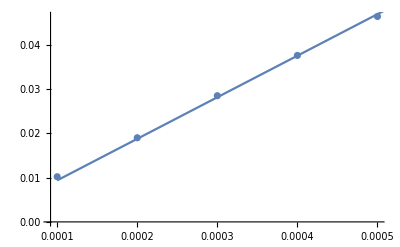

```mathematica
d9DataPhysicalY={{0.0001,0.0011},{0.0002,0.0023},{0.0003,0.0036},{0.0004,0.0048}};
d9DataPhysicalTotal={{0.0001,0.0102},{0.0002,0.0190},{0.0003,0.0285},{0.0004,0.0376},{0.0005,0.0464}};
nlmdPhysTod9=NonlinearModelFit[d9DataPhysicalTotal,{a x^1},{a},x]
nlmdPhysTod9["EstimatedVariance"]
Show[ListPlot[d9DataPhysicalTotal],Plot[nlmdPhysTod9[x],{x,0.0001,0.005}]]
```

#### d_11 polynomials

FittedModel[105.091 x]

3.96364×10^-7

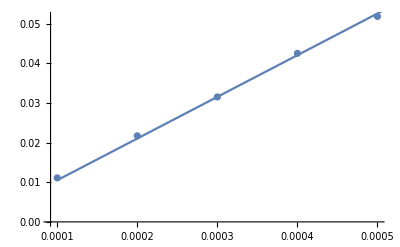

```mathematica
d11DataPhysicalY={{0.0001,0.0013},{0.0002,0.0026},{0.0003,0.0035},{0.0004,0.0049},{0.0005,0.0065}};
d11DataPhysicalTotal={{0.0001,0.0111},{0.0002,0.0217},{0.0003,0.0315},{0.0004,0.0425},{0.0005,0.0518}};
nlmdPhysTod11=NonlinearModelFit[d11DataPhysicalTotal,{a x^1},{a},x]
nlmdPhysTod11["EstimatedVariance"]
Show[ListPlot[d11DataPhysicalTotal],Plot[nlmdPhysTod11[x],{x,0.0001,0.005}]]
```

#### d_13 polynomials

FittedModel[130.4 x]

8.955×10^-7

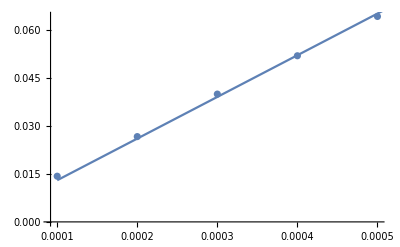

```mathematica
d13DataPhysicalY={{0.0001,0.0016},{0.0002,0.0031},{0.0003,0.0050},{0.0004,0.0064},{0.0005,0.0079}};
d13DataPhysicalTotal={{0.0001,0.0143},{0.0002,0.0267},{0.0003,0.0400},{0.0004,0.0520},{0.0005,0.0643}};
nlmdPhysTod13=NonlinearModelFit[d13DataPhysicalTotal,{a x^1},{a},x]
nlmdPhysTod13["EstimatedVariance"]
Show[ListPlot[d13DataPhysicalTotal],Plot[nlmdPhysTod13[x],{x,0.0001,0.005}]]
```

#### d_15 polynomials

FittedModel[144.182 x]

7.32955×10^-7

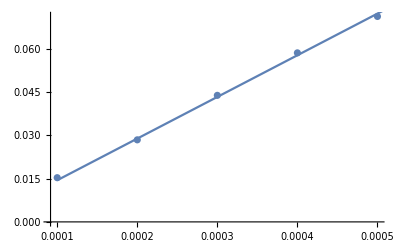

```mathematica
d15DataPhysicalY={{0.0001,0.0018},{0.0002,0.0033},{0.0003,0.0051},{0.0004,0.0075},{0.0005,0.0092}};
d15DataPhysicalTotal={{0.0001,0.0153},{0.0002,0.0284},{0.0003,0.0438},{0.0004,0.0585},{0.0005,0.0711}};
nlmdPhysTod15=NonlinearModelFit[d15DataPhysicalTotal,{a x^1},{a},x]
nlmdPhysTod15["EstimatedVariance"]
Show[ListPlot[d15DataPhysicalTotal],Plot[nlmdPhysTod15[x],{x,0.0001,0.005}]]
```

### Quality of a magic state when growing from d_1 to d_2

```mathematica
(*Physical |H> state prep polynomials*)
pLdist3[p_]:=342*p^2;
pLd5[p_]:=44964*p^3;
pLd7[p_]:=3.16824651*10^6*p^4;
(*Polynomials for growing a physical magic state to distances 9 to 15*)
PolyPhystod9[p_]:=94*p;
PolyPhystod11[p_]:=105*p;
PolyPhystod13[p_]:=130*p;
PolyPhystod15[p_]:=144*p;
(*Polynomials for the color code logical error rate*)
pLcolorCoded5[p_]:=1.869169911951*10^7* p^3;
pLcolorCoded7[p_]:=1.14099418669480*10^10* p^4;
pLcolorCoded9[p_]:=6.263653380559652*10^12* p^5;
pLcolorCoded11[p_]:=3.2408754697234595*10^15* p^6;
pLcolorCoded13[p_]:=9.794312581413016*10^16* p^6.6;
pLcolorCoded15[p_]:=2.566369337434091*10^18* p^7.2;
```

#### Growing to d_9

```mathematica
(*Growing from Subscript[d, 5]*)
PolyPhystod9[pLcolorCoded5[10^-4]]
PolyPhystod9[pLcolorCoded5[2*10^-4]]
PolyPhystod9[pLcolorCoded5[3*10^-4]]
PolyPhystod9[pLcolorCoded5[4*10^-4]]
PolyPhystod9[pLcolorCoded5[5*10^-4]]
```

0.00175702

0.0140562

0.0474395

0.112449

0.219627

```mathematica
N[PolyPhystod9[pLd5[10^-4]]]
N[PolyPhystod9[pLd5[2*10^-4]]]
N[PolyPhystod9[pLd5[3*10^-4]]]
N[PolyPhystod9[pLd5[4*10^-4]]]
N[PolyPhystod9[pLd5[5*10^-4]]]
```

4.22662×10^-6

0.0000338129

0.000114119

0.000270503

0.000528327

```mathematica
N[PolyPhystod9[1*10^-4]]
N[PolyPhystod9[5*10^-4]]
```

0.0094

0.047

```mathematica
(*Growing from Subscript[d, 7]*)
PolyPhystod9[pLcolorCoded7[10^-4]]
PolyPhystod9[pLcolorCoded7[2*10^-4]]
PolyPhystod9[pLcolorCoded7[3*10^-4]]
PolyPhystod9[pLcolorCoded7[4*10^-4]]
PolyPhystod9[pLcolorCoded7[5*10^-4]]
```

0.000107253

0.00171606

0.00868753

0.0274569

0.0670334

#### Growing to d_11

#### Growing to d_13

#### Growing to d_15

## Mathematical relations

```mathematica
X={{0,1},{1,0}};
Z={{1,0},{0,-1}};
Y={{0,-I},{I,0}};
T={{Cos[Pi/8],-Sin[Pi/8]},{Sin[Pi/8],Cos[Pi/8]}};
Tdagger={{Cos[Pi/8],Sin[Pi/8]},{-Sin[Pi/8],Cos[Pi/8]}};
```

```mathematica
FullSimplify[T.X.Tdagger]//MatrixForm
```

(-1/(√2) | 1/(√2)
1/(√2) | 1/(√2))

```mathematica
FullSimplify[Tdagger.X.T]//MatrixForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

```mathematica
FullSimplify[T.Z.Tdagger]//MatrixForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

```mathematica
FullSimplify[Tdagger.Z.T]//MatrixForm
```

(1/(√2) | -1/(√2)
-1/(√2) | -1/(√2))